# Poisson Summation Formula trick

## Taboo Transition density for t ϵ [(n-1)/n,1]

### Fourier transform

Defining the taboo transition probability for the final transition

```mathematica
f[y_]:=(1-Exp[-2n(g2-y)(g1-x)])PDF[NormalDistribution[0,1/(√n)],y-x]If[y<g2,1,0]
```

To analyse the case where the Riemann sum grid lies exactly on the boundary, we do a change of variable, phrasing the transition probability in terms of distance from the boundary

```mathematica
f[g2+x]
```

(ⅇ^(-(g2^2 n)/2) (1-ⅇ^(2 n (g1-x) x)) √n If[g2+x<g2,1,0])/(√(2 π))

Shifted boundary lying θ away from the boundary. z ϵ [0,∞). θ ϵ [0,h]. This is a change of variable g_2-y maps to z + θ. This allows for generalisation to h/2 type shifts. It turns out any other shift aside from h/2 will cause divergence.

```mathematica
f3[z_]:=(1-Exp[-2n( z+θ)(g1-x)])PDF[NormalDistribution[0,1/(√n)],g2-(z+ θ)-x]If[z+ θ>0,1,0]
```

Fourier transform of f_(n,x,θ)

```mathematica
Timing[FullSimplify[Assuming[n>0 &&g1>0 && g2>0 && Element[g1, Reals] && Element[g2, Reals]&& Element[x, Reals] && Element[n, Reals] && Element[s, Reals],FourierTransform[f3[y],y,s,FourierParameters->{0,-2Pi}]],n>0 &&g1>0 && g2>0 && Element[g1, Reals] && Element[g2, Reals]&& Element[x, Reals] && Element[n, Reals] && Element[s, Reals]]]
```

{24.9688,1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))}

```mathematica
fhat[s_]:=1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))
```

The Riemann sum error is equal to the sum of the real part of the Fourier coefficients at the tail. There appears to be no gain from analysing only the real part. Changing θ appears to change the smoothness of the convergence behaviour also.

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)])) ]],{s,1,20,1}],
Table[Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))] ,{s,1,20,1}]

}, PlotRange->Full,PlotLegends->{ "Real FT","Abs FT"}],{{x,0},-3,g1},{{g1,0.6},0.5,3},{{g2,0.6},0.5,3},{{θ,0.3},0,1},{{n,3},3,20,1},ControlPlacement->Left]
```

### Asymptotic expansions

Using two expansions: 1. erf(z) ~ Exp[-z^2]/(√π z) and 2. erfz(-z)-2 ~ (-Exp[-z^2])/(√π z). These expansions are only valid for |Ph[z]|  <(3π)/2.   Let z_1= (n(x-g_2)+2π ⅈ s)/(√(2n)), z_2=(n(g_2-2 g_1+x )- 2π ⅈ s)/(√(2n)). Let z_1^*=-z_1= (n(g_2-x)-2π ⅈ s)/(√(2n))and z_2^*=-z_2=(n(2 g_1-g_2-x)+2π ⅈ s)/(√(2n)). Both the real parts of z_1^*and z_2^* ensure that |Ph[z]|  <(3π)/2

```mathematica
{Series[Erfc[-z],{z,∞,1}],Series[-2+ Erfc[-z],{z,∞,1}]}
```

{2+ⅇ^(-z^2) (-1/(√π z)+O[1/z]^2),ⅇ^(-z^2) (-1/(√π z)+O[1/z]^2)}

Hence we replace Erfc[z_1] = Erfc[-z_1^*] ~ 2 - Exp[-z_1^(*2)]/(√π z_1^*)=2 + Exp[-z_1^2]/(√π z_1) and -2 + Erfc[z_2] = -2 + Erfc[-z_2^*] ~ Exp[-z_2^(*2)]/(√π(-z_2^*))=Exp[-z_2^2]/(√π z_2)

```mathematica
z1 := (n (x-g2)+2 ⅈ π s)/(√(2n))
z2:= (n (-2 g1+g2+x)-2 ⅈ π s)/(√(2 n))
```

```mathematica
ln1 := ⅇ^(-2 g1 n (g2+x) + 4 ⅈ π s x+2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x)))/n)
ln2 := ⅇ^(-2 g1 n (g2+x)+2 g1^2 n+4 ⅈ g1 π s+2 g2 n x-(2 π s (π s+ⅈ n (g2+x)))/n)
```

```mathematica
ln1//Simplify
```

ⅇ^(-(2 π s (ⅈ g2 n+π s-ⅈ n x))/n)

```mathematica
{ln1 ⅇ^(-z1^2) ,ln2 ⅇ^(-z2^2)}//Simplify
```

{ⅇ^(-1/2 n (g2-x)^2),ⅇ^(-1/2 n (g2-x)^2)}

```mathematica
{1/z1+1/z2,ComplexExpand[1/Abs[z1]+1/Abs[z2]]}//Simplify
```

{(2 √2 n^(3/2) (g1-x))/((2 g1 n-g2 n+2 ⅈ π s-n x) (-g2 n+2 ⅈ π s+n x)),√2 (n^2)^(1/4) (1/(√(4 π^2 s^2+n^2 (g2-x)^2))+1/(√(4 π^2 s^2+n^2 (-2 g1+g2+x)^2)))}

The error of these expansions is bounded above by |(ⅇ^(-z^2))/(√π z^3)|(see eqn 2.09 and 2.10 of Asymptotics and special functions [Olver]). We bound this above by |(ⅇ^(-z^2))/(√π z)|, and so we get two times the error - we need to be careful here we absolute value signs. The error explodes when θ = π/2, which corresponds to Re(z) = 0, i.e. x = g_1. Factorising the expansions yields a (g-x), which causes both the difference between the erfc and also the asymptotic exapansions to go to zero.

```mathematica
Manipulate[LogPlot[{Abs[Erfc[a ⅇ^(ⅈ θ)]-(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π a ⅇ^(ⅈ θ))],Abs[(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π(a ⅇ^(ⅈ θ))^3)]},{θ,-2π,2π},PlotLegends->{"Expansion error", "First term"}, PlotLabel->"Erfc expansion error"],{a,1,5},ControlPlacement->Left]
```

Phase agnostic expansion

```mathematica
Manipulate[LogPlot[{Abs[Erfc[a ⅇ^(ⅈ θ)]],Abs[1 - (√((a ⅇ^(ⅈ θ))^2))/(a ⅇ^(ⅈ θ))+(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π a ⅇ^(ⅈ θ))]+Abs[(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π(a ⅇ^(ⅈ θ))^3)]},{θ,-π,π},PlotLegends->{"True", "Expansion"}, PlotLabel->"Erfc expansion "],{a,1,5},ControlPlacement->Left]
```

```mathematica
Manipulate[LogPlot[{Abs[Erfc[a ⅇ^(ⅈ θ)]-(1 - (√((a ⅇ^(ⅈ θ))^2))/(a ⅇ^(ⅈ θ))+(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π a ⅇ^(ⅈ θ)))],Abs[(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π(a ⅇ^(ⅈ θ))^3)]},{θ,-2π,2π},PlotLegends->{"full phase Expansion error", "basic expansion error","Error bound"}, PlotLabel->"Erfc expansion error"],{a,0.1,5},ControlPlacement->Left]
```

```mathematica
Manipulate[LogPlot[{Abs[Erfc[a ⅇ^(ⅈ θ)]-(1 - (√((a ⅇ^(ⅈ θ))^2))/(a ⅇ^(ⅈ θ))+(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π a ⅇ^(ⅈ θ)))],(If[Abs[θ] <π/4,1,0]/2+If[Abs[θ] ≥ π/4,1,0]) Abs[(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π(a ⅇ^(ⅈ θ))^3)]},{θ,-2π,2π},PlotLegends->{"full phase Expansion error", "basic expansion error","Error bound"}, PlotLabel->"Erfc expansion error"],{a,1,5},ControlPlacement->Left]
```

One of the terms becomes (2n)/((n^2(g2 - x))^2+4 π^2 s^2)

```mathematica
1/ComplexExpand[Abs[z1^2]] // Factor
```

(2 √(n^2))/(g2^2 n^2+4 π^2 s^2-2 g2 n^2 x+n^2 x^2)

The multiplier error from the first expansion is

```mathematica
ComplexExpand[Abs[ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n)ⅇ^(4 ⅈ π s x+2 g1 n (g2+x))]]
```

ⅇ^(-(2 π^2 s^2)/n)

Looking at the second term, which is slightly more annoying. (n^2(x + g_2- 2 g_1))^2+4 π^2 s^2

```mathematica
Expand[n^2(x + g2 - 2g1)^2]
```

4 g1^2 n^2-4 g1 g2 n^2+g2^2 n^2-4 g1 n^2 x+2 g2 n^2 x+n^2 x^2

```mathematica
1/ComplexExpand[Abs[z2^2]] //Factor
```

(2 √(n^2))/(4 g1^2 n^2-4 g1 g2 n^2+g2^2 n^2+4 π^2 s^2-4 g1 n^2 x+2 g2 n^2 x+n^2 x^2)

The multiplier is no longer so simple, and has dependence on x. Simplifying gives Exp( 2n g_1(g_1-g_2)  )Exp[-2 π^2 s^2/n]Exp[2nx(g2  - g1)]

```mathematica
ComplexExpand[Abs[ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n)ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x)]]
```

ⅇ^(2 g1^2 n-(2 π^2 s^2)/n+2 g2 n x-2 g1 n (g2+x))

We see that the integral is bounded uniformly in n

```mathematica
∫_(-∞)^g1 (g1-x)PDF[NormalDistribution[0,(n-1)/n],x] ⅇ^(2K(g1-x))ⅆx//FullSimplify
```

ConditionalExpression[1/(2 n^3 √π)ⅇ^(2 K (g1+(K (-1+n)^2)/n^2)) ((-1+n) (√2 ⅇ^(-((2 K (-1+n)^2+g1 n^2)^2)/(2 (-1+n)^2 n^2)) n^2+√(n^2/(-1+n)^2) (2 K (-1+n)^2+g1 n^2) √π)+n (2 K (-1+n)^2+g1 n^2) √π Erf[(2 K (-1+n)^2+g1 n^2)/(√2 (-1+n) n)]),Re[n^2/(-1+n)^2]>0||(Re[n^2/(-1+n)^2]≥0&&Re[K]>0)]

```mathematica
Manipulate[Plot[(g1-x)PDF[NormalDistribution[0,(n-1)/n],x]If[a==1,ⅇ^(2Kc(g1-x)),1],{x,-3,g1}],{g1,0.5,10},{Kc,0.5,1},{n,2,100,1},{a,{1,0}}]
```

```mathematica
∫_(-∞)^∞ PDF[NormalDistribution[0,√((n-1)/n)],x] ⅇ^(2K(g-x))ⅆx
```

ConditionalExpression[ⅇ^((2 K (K (-1+n)+g n))/n)/(√((-1+n)/n) √(2 π) √(-n/(2 π-2 n π))),Re[n/(-1+n)]≥0&&Re[n/(2-2 n)]<0]

```mathematica
ⅇ^((2 K (K (-1+n)+g n))/n)/(√((-1+n)/n) √(2 π) √(-n/(2 π-2 n π)))//FullSimplify
```

ⅇ^((2 K (K (-1+n)+g n))/n) √((-1+n)/n) √(n/(-1+n))

```mathematica
∫_(-∞)^∞ Abs[g1-x]PDF[NormalDistribution[0,(n-1)/n],x] ⅇ^(2K(g1-x))ⅆx//FullSimplify
```

$Aborted

Left over errors

```mathematica
1/2 ⅇ^(-2 g1 n (g2+x)-(2 (π s)^2)/n)( ⅇ^(2 g1 n (g2+x)) Abs[Exp[-z1^2]/(√π z1) ]+ⅇ^(2 g1^2 n+2 g2 n x) Abs[Exp[-z2^2]/(√π z2)])//FullSimplify
```

$Aborted

### Substitution of asymptotic expansions in Fourier transform

Hence we are left with an exponentially decaying term and the EMSF error

```mathematica
1/2 ⅇ^(-2 g1 n (g2+x)-(2 (π s)^2)/n + ⅈ n (g2+x-θ))( ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) (2  +Exp[-z1^2]/(√π z1) )+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (Exp[-z2^2]/(√π z2)))
```

Looking at just the exponentials after expansion, we can factorise.

```mathematica
(ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) ( Exp[-z1^2]/(√π z1))+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (Exp[-z2^2]/(√π z2)))//Simplify
```

(2 ⅇ^(-(g2^2 n)/2+2 g1 n (g2+x)+(2 π s+ⅈ n x)^2/(2 n)+g2 (2 ⅈ π s+n x)) n^(3/2) √(2/π) (g1-x))/((2 g1 n-g2 n+2 ⅈ π s-n x) (-g2 n+2 ⅈ π s+n x))

```mathematica
ComplexExpand[Re[-(g2^2 n)/2+2 g1 n (g2+x)+(2 π s+ⅈ n x)^2/(2 n)+g2 (2 ⅈ π s+n x)]]+-2 g1 n (g2+x)-(2 (π s)^2)/n//Simplify
```

-1/2 n (g2-x)^2

```mathematica
ComplexExpand[Im[-(g2^2 n)/2+2 g1 n (g2+x)+(2 π s+ⅈ n x)^2/(2 n)+g2 (2 ⅈ π s+n x)]] +  n (g2+x)//Simplify
```

(n+2 π s) (g2+x)

The exponentially decaying terms are also dealt with nicely

```mathematica
{ⅇ^(-2 g1 n (g2+x)-(2 (π s)^2)/n + ⅈ n (g2+x-θ)) ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)),ⅇ^(-2 g1 n (g2+x)-(2 (π s)^2)/n + ⅈ n (g2+x-θ))ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x)}//Simplify
```

{ⅇ^(-(2 π^2 s^2)/n+4 ⅈ π s x+ⅈ n (g2+x-θ)),ⅇ^(2 g1^2 n+4 ⅈ g1 π s-(2 π^2 s^2)/n+2 g2 n x-2 g1 n (g2+x)+ⅈ n (g2+x-θ))}

```mathematica
{ⅇ^(-2 g1 n (g2+x)) ⅇ^(2 g1 n (g2+x)),ⅇ^(-2 g1 n (g2+x))ⅇ^(2 g1^2 n+2 g2 n x)}//Simplify
```

{1,ⅇ^(2 (g1-g2) n (g1-x))}

Multiplying the stuff in the front with the exponential terms

```mathematica
1/2 ⅇ^(-2 g1 n (g2+x)-(2 (π s)^2)/n + ⅈ n (g2+x-θ))(2 ⅇ^(-(g2^2 n)/2+2 g1 n (g2+x)+(2 π s+ⅈ n x)^2/(2 n)+g2 (2 ⅈ π s+n x)) n^(3/2) √(2/π) (g1-x))/((2 g1 n-g2 n+2 ⅈ π s-n x) (-g2 n+2 ⅈ π s+n x))//Simplify
```

-(ⅇ^(-(g2^2 n)/2+2 ⅈ π s x+g2 (2 ⅈ π s+n (ⅈ+x))-1/2 n (-2 ⅈ x+x^2+2 ⅈ θ)) n^(3/2) √(2/π) (-g1+x))/((g2 n-2 ⅈ π s-n x) (-2 g1 n+g2 n-2 ⅈ π s+n x))

Hence our error becomes

```mathematica
ⅇ^(-(2 π^2 s^2)/n+4 ⅈ π s x+ⅈ n (g2+x-θ)) -(ⅇ^(-(g2^2 n)/2+2 ⅈ π s x+g2 (2 ⅈ π s+n (ⅈ+x))-1/2 n (-2 ⅈ x+x^2+2 ⅈ θ)) n^(3/2) √(2/π) (-g1+x))/((g2 n-2 ⅈ π s-n x) (-2 g1 n+g2 n-2 ⅈ π s+n x))
```

Finding a lower bound of the absolute value of the denominator, we get 4 π^2 s^2

```mathematica
ComplexExpand[ Abs[(g2 n-2 ⅈ π s-n x) (-2 g1 n+g2 n-2 ⅈ π s+n x)]]
```

√(4 π^2 s^2+(g2 n-n x)^2) √(4 π^2 s^2+(-2 g1 n+g2 n+n x)^2)

Taking only the real part of the exponential, since we are taking absolute value of the exponential. -n/2(g_2-x)^2

```mathematica
ComplexExpand[Re[-(g2^2 n)/2+2 ⅈ π s x+g2 (2 ⅈ π s+n (ⅈ+x))-1/2 n (-2 ⅈ x+x^2+2 ⅈ θ)]]
```

-(g2^2 n)/2+g2 n x-(n x^2)/2

Hence we are left with the two major sources of error, which agrees with the EMSF. We see that boundary shifting makes no difference for the last transition.

```mathematica
ⅇ^(-(2 π^2 s^2)/n)+ (n^(3/2) √(2/π) (g1-x)ⅇ^(-n/2(g2 -x)^2))/(4 π^2 s^2)
```

Since the PSF error is equal to ∑_(k ≠ 0) FT[k/h], we sum across all the integers

```mathematica
2∑_(k=1)^∞ k^-2
```

π^2/3

Since 2 ⅇ^(-2π^2(2^2))=1.0245×10^-34is immaterial, we ignore the rest of the exponential tail terms. Hence the final error is

```mathematica
ⅇ^(-(2 π^2)/(n h^2))+ (n^(3/2) √(2/π) (g1-x)ⅇ^(-n/2(g2 -x)^2))/12 h^2
```

### Exponentially/polynomial decaying terms, using higher order expansion

```mathematica
Series[Erfc[z],{z,∞,5}]
```

ⅇ^(-z^2) (1/(√π z)-1/(2 √π z^3)+3/(4 √π z^5)+O[1/z]^6)

Use Olver to find that constant.

```mathematica
Manipulate[LogPlot[{Abs[Erfc[a ⅇ^(ⅈ θ)]-(1 - (√((a ⅇ^(ⅈ θ))^2))/(a ⅇ^(ⅈ θ))+(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π a ⅇ^(ⅈ θ))-(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(2 √π(a ⅇ^(ⅈ θ))^3))], Abs[(5 ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π(a ⅇ^(ⅈ θ))^5)]},{θ,-2π,2π},PlotLegends->{"full phase Expansion error", "Error bound"}, PlotLabel->"Erfc expansion error"],{a,1,5},ControlPlacement->Left]
```

Here we get 4th order error in s

```mathematica
Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Exp[-z1^2]/(√π z1^3)+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (+2+Exp[-z2^2]/(√π z2^3)))]
```

1/2 ⅇ^Re[-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x)))/n] Abs[(2 ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)-(2 ⅈ π s+n (-g2+x))^2/(2 n)) n^(3/2) √(2/π))/(2 ⅈ π s+n (-g2+x))^3+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (2+(2 ⅇ^(-(-2 ⅈ π s+n (-2 g1+g2+x))^2/(2 n)) n^(3/2) √(2/π))/(-2 ⅈ π s+n (-2 g1+g2+x))^3)]

```mathematica
Series[Abs[ⅇ^(4 ⅈ π s x-(2 π s (π s+ⅈ n (g2+x)))/n) Exp[-z1^2]/(√π z1^3)+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x)))/n) (Exp[-z2^2]/(√π z2^3))],{s,∞,2}]
```

Abs[(2 ⅇ^(-(g2^2 n)/2+g2 n x-(n x^2)/2) n^(3/2) √(2/π))/(2 ⅈ π s+n (-g2+x))^3+(2 ⅇ^(-(g2^2 n)/2+g2 n x-(n x^2)/2) n^(3/2) √(2/π))/(-2 ⅈ π s+n (-2 g1+g2+x))^3]

```mathematica
ComplexExpand[Abs[1/(2 ⅈ π s+n (-g2+x))^3+1/(-2 ⅈ π s+n (-2 g1+g2+x))^3]]//Simplify
```

√(((8 π^3 s^3-6 n^2 π s (g2-x)^2)/((4 π^2 s^2+n^2 (g2-x)^2)^3)+(-8 π^3 s^3+6 n^2 π s (-2 g1+g2+x)^2)/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^3))^2+((12 n π^2 s^2 (g2-x)+n^3 (-g2+x)^3)/((4 π^2 s^2+n^2 (g2-x)^2)^3)+(-12 n π^2 s^2 (-2 g1+g2+x)+n^3 (-2 g1+g2+x)^3)/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^3))^2)

```mathematica
Series[√(((8 π^3 s^3-6 n^2 π s (g2-x)^2)/((4 π^2 s^2+n^2 (g2-x)^2)^3)+(-8 π^3 s^3+6 n^2 π s (-2 g1+g2+x)^2)/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^3))^2+((12 n π^2 s^2 (g2-x)+n^3 (-g2+x)^3)/((4 π^2 s^2+n^2 (g2-x)^2)^3)+(-12 n π^2 s^2 (-2 g1+g2+x)+n^3 (-2 g1+g2+x)^3)/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^3))^2),{s,∞,4}]
```

(3 √((g1 n-n x)^2))/(8 π^4 s^4)+O[1/s]^5

```mathematica
Manipulate[
LogLogPlot[{
Abs[1/(2 ⅈ π s+n (-g2+x))^3+1/(-2 ⅈ π s+n (-2 g1+g2+x))^3],10^-9/s^4
}
,{s,1,100}, PlotRange->Full, PlotLabel->"True vs Approximation", PlotLegends->{"Tail upper bound","1/s^4"}],{x,-3,g1},{g1,0.5,3},{g2,0.5,3},{n,1,20,1},{a,0.5,1},ControlPlacement->Left]
```

```mathematica
Manipulate[
LogLogPlot[{
1/2 ⅇ^Re[-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x)))/n] Abs[(2 ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)-(2 ⅈ π s+n (-g2+x))^2/(2 n)) n^(3/2) √(2/π))/(2 ⅈ π s+n (-g2+x))^3+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (2+(2 ⅇ^(-(-2 ⅈ π s+n (-2 g1+g2+x))^2/(2 n)) n^(3/2) √(2/π))/(-2 ⅈ π s+n (-2 g1+g2+x))^3)],10^-9/s^4
}
,{s,1,100}, PlotRange->Full, PlotLabel->"True vs Approximation", PlotLegends->{"Tail upper bound","1/s^4"}],{x,-3,g1},{g1,0.5,3},{g2,0.5,3},{n,1,20,1},{a,0.5,1},ControlPlacement->Left]
```

Estimate for B_2(s)

```mathematica
ComplexExpand[1/2 ⅇ^(-(2 (π s)^2)/n) (Abs[Exp[-z1^2]/(√π z1^3)]+ⅇ^(2n(g1-g2)(g1-x)) Abs[(Exp[-z2^2]/(√π z2^3))])]//Simplify
```

(n^2)^(3/4) √(2/π) ((ⅇ^((2 π^2 s^2)/n-n (g2-x)^2) √(ⅇ^(-(4 π^2 s^2)/n+n (g2-x)^2)))/((4 π^2 s^2+n^2 (g2-x)^2)^(3/2))+(ⅇ^(-1/2 n (g2-x)^2))/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^(3/2)))

```mathematica
Simplify[(n^2)^(3/4) √(2/π) ((ⅇ^((2 π^2 s^2)/n-n (g2-x)^2) √(ⅇ^(-(4 π^2 s^2)/n+n (g2-x)^2)))/((4 π^2 s^2+n^2 (g2-x)^2)^(3/2))+(ⅇ^(-1/2 n (g2-x)^2))/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^(3/2))), -(4 π^2 s^2)/n+n (g2-x)^2 >0]
```

ⅇ^(-1/2 n (g2-x)^2) √(2/π) (1/((4 π^2 s^2+n^2 (g2-x)^2)^(3/2))+1/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^(3/2))) Abs[n]^(3/2)

Using a higher order expansion

```mathematica
ComplexExpand[Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x)))/n) ](Abs[ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) ]Abs[Exp[-z1^2]/(√π z1^5)]+Abs[ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x)] Abs[(Exp[-z2^2]/(√π z2^5))])] //Simplify
```

2 ⅇ^(-1/2 n (g2-x)^2) (n^2)^(5/4) √(2/π) (1/((4 π^2 s^2+n^2 (g2-x)^2)^(5/2))+1/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^(5/2)))

We get 5 order error now.

```mathematica
Series[ComplexExpand[Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x)))/n) ](Abs[ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) ]Abs[Exp[-z1^2]/(√π z1^5)]+Abs[ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x)] Abs[(Exp[-z2^2]/(√π z2^5))])] //Simplify,{s,∞,5}]
```

(ⅇ^(-1/2 n (g2-x)^2) (n^2)^(5/4))/(4 √2 π^(11/2) s^5)+O[1/s]^6

### Final approximation comparison

Plot of our approximation vs true. We have multiplied by two to account for all error terms.

```mathematica
Manipulate[
LogLogPlot[{
n/(2 π^2 s^2)(g1-x)PDF[NormalDistribution[0,1/(√n)],g2-x] +ⅇ^(-(2 π^2 s^2)/n)(1+ⅇ^(2n(g1-g2)(g1-x)))+n/(4 π^3 s^3)PDF[NormalDistribution[0,1/(√n)],g2-x]/.s-> k n^a,
Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))]/.s-> k n^a /. θ-> 0
}
,{n,1,200}, PlotRange->Full, PlotLabel->"True vs Approximation", PlotLegends->{"Vin upper bound","True error"}],{x,-3,g1},{g1,0.5,3},{g2,0.5,3},{k,1,20,1},{a,0.5,1},ControlPlacement->Left]
```

There is a critical frequency s* where the FT behaves like the FT of the normal density in [-s*,s*], then switches to the FT of the cutoff normal density. As we increase n, s* also increases. For fixed n,g There is a small region [x*-,x*+] for x  where the polynomial part becomes apparent.

```mathematica
Manipulate[LogPlot[{
n/(2 π^2 s^2)(g1-x)PDF[NormalDistribution[0,1/(√n)],g2-x],
ⅇ^(-(2 π^2 s^2)/n),
Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))],
Abs[Re[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))]]},{s,-4,4}, PlotRange->Full, PlotLabel->"FT upper bound", PlotLegends->{"Polynomial part","exp part","ABS FT","Re FT"},PlotStyle->{Blue,Blue,Red,Dashed}],{{n,46},1,50},{{x,0.157},-3,g1},{g1,0.5,3},{g2,0.5,3},ControlPlacement->Left]
```

```mathematica
Manipulate[LogLogPlot[{n/(2 π^2 s^2)(g1-x)PDF[NormalDistribution[0,1/(√n)],g2-x] +ⅇ^(-(2 π^2 s^2)/n),
n/(2 π^2 s^2)(g1-x)PDF[NormalDistribution[0,1/(√n)],g2-x],
Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))]},{s,-4,4}, PlotRange->Full, PlotLabel->"True vs Approximation", PlotLegends->{"Vin upper bound","Polynomial part","True"}],{n,1,50},{x,-3,g1},{g1,0.5,3},{g2,0.5,3},ControlPlacement->Left]
```

My Ansatz. If α = 0.5, the exponential in s is just a constant. Eventually the first term becomes small enough so that the we are left with the exponential constant, i.e. no convergence. There is a point n* were the convergence is determined by one of the terms. On the left of n*, the EMSF error is dominant. On the right of n*, the Normal error is dominant. As we move α higher, n* moves higher, so most of the error is determined by the EMSF.

```mathematica
Manipulate[
LogLogPlot[{
n/(2 π^2 s^2)(g1-x)PDF[NormalDistribution[0,1/(√n)],g2-x] +ⅇ^(-(2 π^2 s^2)/n)/.s-> k n^a,
Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))]/.s-> k n^a /. θ-> 0
}
,{n,1,200}, PlotRange->Full, PlotLabel->"True vs Approximation", PlotLegends->{"Vin upper bound","True error"}],{x,-3,g1},{g1,0.5,3},{g2,0.5,3},{k,1,20,1},{a,0.5,1},ControlPlacement->Left]
```

```mathematica
Simplify[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))/. g2 -> g1 /. g1-> x /. θ -> 0,n>0 ]
```

1/2 ⅇ^(-(2 π^2 s^2)/n) (-2+Erfc[-(ⅈ √2 π s)/(√n)]+Erfc[(ⅈ √2 π s)/(√n)])

```mathematica
Erfc[x] - (2 - Erfc[-x]) //Simplify
```

-2+Erfc[-x]+Erfc[x]

```mathematica
Manipulate[
LogLogPlot[{
Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))]-(n/(2 π^2 s^2)(g1-x)PDF[NormalDistribution[0,1/(√n)],g2-x] +ⅇ^(-(2 π^2 s^2)/n))/.s-> k n^a /. θ-> 0
}
,{n,1,200}, PlotRange->Full, PlotLabel->"True vs Approximation", PlotLegends->{"Vin upper bound","True error"}],{x,-3,g1},{g1,0.5,3},{g2,0.5,3},{k,1,20,1},{a,0.5,1},ControlPlacement->Left]
```

### Alternative Fourier method

The rest of the stuff

```mathematica
f[z_]:=(1-Exp[-2n z(g1-x)])PDF[NormalDistribution[0,1/(√n)],g2-z-x]If[z>0,1,0]
```

```mathematica
D[f[z],{z,2}]//Simplify
```

Piecewise[{{(ⅇ^(-1/2 n (4 (g1-x) z+(-g2+x+z)^2)) n^(3/2) (1-4 g1^2 n-g2^2 n-2 g2 n x-n x^2+4 g1 n (g2+x-z)+2 g2 n z+2 n x z-n z^2+ⅇ^(2 n (g1-x) z) (-1+g2^2 n-2 g2 n (x+z)+n (x+z)^2)))/(√(2 π)), z>0}, {0, True}}]

The polynomial s^2 terms have to cancel out with the error function.

```mathematica
FourierTransform[(ⅇ^(-1/2 n (4 (g1-x) z+(-g2+x+z)^2)) n^(3/2) (1-4 g1^2 n-g2^2 n-2 g2 n x-n x^2+4 g1 n (g2+x-z)+2 g2 n z+2 n x z-n z^2+ⅇ^(2 n (g1-x) z) (-1+g2^2 n-2 g2 n (x+z)+n (x+z)^2)))/(√(2 π))If[z>0,1,0],z,s,FourierParameters->{0, -2*Pi}]
```

-ⅇ^(-1/2 n (g2-x)^2) √(2/π) (g1 n^(3/2)-√2 ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2+√2 ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2-n^(3/2) x+√2 ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2 Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]+√2 ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2 Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)])

Triangle inequality

```mathematica
ⅇ^(-1/2 n (g2-x)^2) √(2/π)( (g1 -x)n^(3/2) +√2 π^(5/2) s^2 Abs[ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) - ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))]+√2 π^(5/2) s^2 Abs[ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n))  Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]+ ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))  Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)]])
```

```mathematica
{ComplexExpand[Re[ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) - ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))]],ComplexExpand[Abs[ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) - ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))]]//Simplify}//Simplify
```

{ⅇ^(-(2 π^2 s^2)/n) (-ⅇ^(1/2 n (-2 g1+g2+x)^2) Cos[2 π s (2 g1-g2-x)]+ⅇ^(1/2 n (g2-x)^2) Cos[2 π s (g2-x)]),√(ⅇ^(-(4 π^2 s^2)/n) (ⅇ^(n (g2-x)^2)+ⅇ^(n (-2 g1+g2+x)^2)-2 ⅇ^(n (2 g1^2+g2^2+x^2-2 g1 (g2+x))) Cos[4 π s (g1-x)]))}

```mathematica
Series[Abs[ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n))  Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]+ ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))  Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)]],{s,∞,3}]//Simplify
```

$Aborted

```mathematica
Series[Erf[z],{z,∞,3}]
```

1+ⅇ^(-z^2) (-1/(√π z)+1/(2 √π z^3)+O[1/z]^4)

```mathematica
z1 :=(g2 n-2 ⅈ π s-n x)/(√2 √n)
z2:=(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)
l1:=ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n))
l2:=ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))
```

```mathematica
√2 π^(5/2) s^2 Series[l1(1 + ⅇ^(-z1^2)(-1/(√π z1))) + l2(1 + ⅇ^(-z2^2)(-1/(√π z2)) )//Simplify,{s,∞,4}]//Simplify
```

√2 (ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))+ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n))) π^(5/2) s^2+(n^(3/2) (-g1+x)-(ⅈ (g1-g2) n^(5/2) (g1-x))/(π s)+(n^(7/2) (g1-x) (4 g1^2+3 g2^2+x^2-2 g1 (3 g2+x)))/(4 π^2 s^2)+O[1/s]^3)

```mathematica
√2 π^(5/2) s^2 Series[l1(1 + ⅇ^(-z1^2)(-1/(√π Abs[z1^3]))) + l2(1 + ⅇ^(-z2^2)(-1/(√π Abs[z2^3])) )//Simplify,{s,∞,4}]//Simplify
```

√2 π^(5/2) s^2 (ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))+ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n))-(2 √(2/π))/Abs[(g2 n-2 ⅈ π s-n x)^3/n^(3/2)]-(2 √(2/π))/Abs[(2 g1 n-g2 n+2 ⅈ π s-n x)^3/n^(3/2)])

```mathematica
{l1 ⅇ^(-z1^2),l2 ⅇ^(-z2^2)}//Simplify
```

{1,1}

```mathematica
√2 π^(5/2) s^2  ComplexExpand[Simplify[1/Abs[z1^3]+1/Abs[z2^3] ]] //Simplify
```

4 (n^2)^(3/4) π^(5/2) s^2 (1/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^(3/2))+1/((4 π^2 s^2+(g2 n-n x)^2)^(3/2)))

```mathematica
4 (n^2)^(3/4) π^(5/2) s^2 (1/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^(3/2))+1/((4 π^2 s^2+(g2 n-n x)^2)^(3/2)))/.g1->g2//Simplify
```

(8 (n^2)^(3/4) π^(5/2) s^2)/((4 π^2 s^2+(g2 n-n x)^2)^(3/2))

```mathematica
4 (n^2)^(3/4) π^(5/2) s^2 (1/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^(3/2))+1/((4 π^2 s^2+(g2 n-n x)^2)^(3/2)))//Together
```

(4 (n^2)^(3/4) π^(5/2) s^2 (4 g1^2 n^2 √(4 π^2 s^2+n^2 (-2 g1+g2+x)^2)-4 g1 g2 n^2 √(4 π^2 s^2+n^2 (-2 g1+g2+x)^2)+g2^2 n^2 √(4 π^2 s^2+n^2 (-2 g1+g2+x)^2)+4 π^2 s^2 √(4 π^2 s^2+n^2 (-2 g1+g2+x)^2)-4 g1 n^2 x √(4 π^2 s^2+n^2 (-2 g1+g2+x)^2)+2 g2 n^2 x √(4 π^2 s^2+n^2 (-2 g1+g2+x)^2)+n^2 x^2 √(4 π^2 s^2+n^2 (-2 g1+g2+x)^2)+g2^2 n^2 √(4 π^2 s^2+(g2 n-n x)^2)+4 π^2 s^2 √(4 π^2 s^2+(g2 n-n x)^2)-2 g2 n^2 x √(4 π^2 s^2+(g2 n-n x)^2)+n^2 x^2 √(4 π^2 s^2+(g2 n-n x)^2)))/((4 π^2 s^2+n^2 (-2 g1+g2+x)^2)^(3/2) (4 π^2 s^2+(g2 n-n x)^2)^(3/2))

```mathematica
Simplify[-√2 π^(5/2) s^2  ComplexExpand[Abs[Simplify[1/z1+1/z2 ]]] ,n >0]
```

-(4 n^(3/2) π^(5/2) s^2 √((g1-x)^2))/(√(4 π^2 s^2+n^2 (-2 g1+g2+x)^2) √(4 π^2 s^2+(g2 n-n x)^2))

```mathematica
Manipulate[LogLogPlot[{
Abs[(g1 -x)n^(3/2)√(2/π)ⅇ^(-1/2 n (g2-x)^2)],
Abs[-ⅇ^(-1/2 n (g2-x)^2) √(2/π) (g1 n^(3/2)-√2 ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2+√2 ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2-n^(3/2) x+√2 ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2 Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]+√2 ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2 Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)])],
Abs[Re[-ⅇ^(-1/2 n (g2-x)^2) √(2/π) (g1 n^(3/2)-√2 ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2+√2 ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2-n^(3/2) x+√2 ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2 Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]+√2 ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2 Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)])]],
ⅇ^(-1/2 n (g2-x)^2) √(2/π)( (g1 -x)n^(3/2) +√2 π^(5/2) s^2 Abs[ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) - ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))]+√2 π^(5/2) s^2 Abs[ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n))  Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]+ ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))  Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)]])},{s,1,50}, PlotLegends-> {"constant","ABS","RE","Triangle"},PlotStyle->{Opacity[a],Opacity[b],Opacity[c],Dashed}],{g1,0.5,2},{g2,0.5,2},{n,1,10},{x,-3,g1},{{a,0.7},0,1},{{b,0.7},0,1},{{c,0.7},0,1},ControlPlacement->Left]
```

```mathematica
Manipulate[LogLogPlot[{
Abs[(g1 -x)n^(3/2)√(2/π)ⅇ^(-1/2 n (g2-x)^2)],
Abs[-ⅇ^(-1/2 n (g2-x)^2) √(2/π) (g1 n^(3/2)-√2 ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2+√2 ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2-n^(3/2) x+√2 ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2 Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]+√2 ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2 Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)])],
Abs[Re[-ⅇ^(-1/2 n (g2-x)^2) √(2/π) (g1 n^(3/2)-√2 ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2+√2 ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2-n^(3/2) x+√2 ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2 Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]+√2 ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n)) π^(5/2) s^2 Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)])]],
ⅇ^(-1/2 n (g2-x)^2) √(2/π)( (g1 -x)n^(3/2) +√2 π^(5/2) s^2 Abs[ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n)) - ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))]+√2 π^(5/2) s^2 Abs[ⅇ^((-g2 n+2 ⅈ π s+n x)^2/(2 n))  Erf[(g2 n-2 ⅈ π s-n x)/(√2 √n)]+ ⅇ^((-2 g1 n+g2 n-2 ⅈ π s+n x)^2/(2 n))  Erf[(2 g1 n-g2 n+2 ⅈ π s-n x)/(√2 √n)]])},{s,1,50}, PlotLegends-> {"constant","ABS","RE","Triangle"},PlotStyle->{Opacity[a],Opacity[b],Opacity[c],Dashed}],{g1,0.5,2},{g2,0.5,2},{n,1,10},{x,-3,g1},{{a,0.7},0,1},{{b,0.7},0,1},{{c,0.7},0,1},ControlPlacement->Left]
```

## Taboo Transition density for t ϵ [0,(n-1)/n)

### EMSF

```mathematica
Evaluate[D[(1-Exp[-2n(g2-x2)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x2-x1](1-Exp[-2n(g0-x0)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x1-x0],{x1,3}] ]/. x1 -> g1 //Simplify
```

(12 ⅇ^(-1/2 n ((g1-x0)^2+(g1-x2)^2)) (g0-2 g1+g2) n^4 (-g0+x0) (-g2+x2))/π

### Fourier transforms

This is the part of the taboo transition density that depends on the x_k position.

```mathematica
f2[x1_]:=(1-Exp[-2n(g2-x2)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x2-x1](1-Exp[-2n(g0-x0)(g1-x1)])PDF[NormalDistribution[0,1/(√n)],x1-x0]If[x1<g1,1,0]
```

From numerical experiments, it is clear that boundary dependent positioning is important to ensure h^4 convergence. Hence we center the density at z = g_1-x_1and then shift z by θ ϵ [0,h] from the boundary also. So x_1=g_1-z_1

```mathematica
f2θ[z_]:=(1-Exp[-2n(g2-x2)(z + θ)])PDF[NormalDistribution[0,1/(√n)],g1 - (z + θ) -x2](1-Exp[-2n(g0-x0)(z + θ)])PDF[NormalDistribution[0,1/(√n)],g1-(z+θ)-x0]If[z +θ>0,1,0]
```

```mathematica
f2[z_]:=(1-Exp[-2n(g2-x2)z])PDF[NormalDistribution[0,1/(√n)],g1 - z -x2](1-Exp[-2n(g0-x0)z ])PDF[NormalDistribution[0,1/(√n)],g1-z-x0]If[z>0,1,0]
```

Fourier transform sitting on the boundary

```mathematica
Timing[
Assuming[n>0 &&g0>0&&g1>0 && g2>0&&θ >0&& Element[θ, Reals]  && Element[g0, Reals] && Element[g1, Reals]&& Element[g2, Reals]&& Element[x0, Reals] && Element[z, Reals] && Element[x2, Reals]&& Element[n, Reals] && Element[s, Reals],
FourierTransform[f2[z],z,s,FourierParameters->{0,-2Pi}]]
]
```

{38.0469,1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π)/(2 √n)-(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π)/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π)/(2 √n)+1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π-1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])/(2 √n))}

The Fourier transform isn’t too bad!

```mathematica
f2hat[s_]:=1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π)/(2 √n)-(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π)/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π)/(2 √n)+1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π-1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])/(2 √n))
```

Simplification allows us to factorise, and get 4 complementary error functions. recall that erfc(z) = 1 - erf(z)

```mathematica
f2hatsimp[s_]:=1/(2 π)n (1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π (1-Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)])-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1)+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1)+1/(2 √n)ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π (1+Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)]))
```

```mathematica
l1:=ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2)))
l2:=ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2))
l3:=ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2)
l4:=ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2))
```

```mathematica
q:=-n/2((g1 - x0)^2 +(g1 - x2)^2)+n/4((g1-x0)+(g1-x2))^2
```

#### Simplifying the exponential terms

L1 term

```mathematica
ComplexExpand[Re[g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))]]
```

g0^2 n-2 g0 g1 n+2 g0 g2 n-2 g1 g2 n+g2^2 n-(π^2 s^2)/n-g0 n x0+2 g1 n x0-g2 n x0-(n x0^2)/4-g0 n x2+2 g1 n x2-g2 n x2+(n x0 x2)/2-(n x2^2)/4

```mathematica
(g0^2 n-2 g0 g1 n+2 g0 g2 n-2 g1 g2 n+g2^2 n-(π^2 s^2)/n-g0 n x0+2 g1 n x0-g2 n x0-(n x0^2)/4-g0 n x2+2 g1 n x2-g2 n x2+(n x0 x2)/2-(n x2^2)/4)-(-n/2((g1 - x0)^2 +(g1 - x2)^2)+n/4((g1-x0)+(g1-x2))^2-(π^2 s^2)/n)//Simplify
```

(g0-2 g1+g2) n (g0+g2-x0-x2)

```mathematica
ComplexExpand[Im[g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))]]/(π s)//Simplify
```

2 g0-2 g1+2 g2-x0-x2

what we define to be q

```mathematica
ComplexExpand[Re[g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))] -(-n/2((g1 - x0)^2 +(g1 - x2)^2)+n/4((g1-x0)+(g1-x2))^2-(π^2 s^2)/n + n(g2 - 2g1 + g0 )(g2 - x2 + g0 - x0)) ]
```

0

L2

```mathematica
ComplexExpand[Re[g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)]]
```

-2 g1 g2 n+g2^2 n-(π^2 s^2)/n+g2 n x0-(n x0^2)/4+2 g1 n x2-g2 n x2-(n x0 x2)/2-(n x2^2)/4

```mathematica
-2 g1 g2 n+g2^2 n-(π^2 s^2)/n+g2 n x0-(n x0^2)/4+2 g1 n x2-g2 n x2-(n x0 x2)/2-(n x2^2)/4 - (-n/2((g1 - x0)^2 +(g1 - x2)^2)+n/4((g1-x0)+(g1-x2))^2-(π^2 s^2)/n)//Simplify
```

-n (2 g1-g2-x0) (g2-x2)

```mathematica
-2 g1 g2 n+g2^2 n-(π^2 s^2)/n+g2 n x0-(n x0^2)/4+2 g1 n x2-g2 n x2-(n x0 x2)/2-(n x2^2)/4 - (-n/2((g1 - x0)^2 +(g1 - x2)^2)+n/4((g1-x0)+(g1-x2))^2-(π^2 s^2)/n + n(g2 - 2g1 +g0 - (g0 - x0))(g2 - x2))//Simplify
```

0

```mathematica
ComplexExpand[Im[g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)]]//FullSimplify
```

π s (-2 g1+2 g2+x0-x2)

L3

```mathematica
ComplexExpand[Re[g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2] ]- (-n/2((g1 - x0)^2 +(g1 - x2)^2)+n/4((g1-x0)+(g1-x2))^2-(π^2 s^2)/n+n (g0-x0) (g0-2 g1+x2))//Simplify
```

0

```mathematica
ComplexExpand[Im[g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2] ]//Simplify
```

π s (2 g0-2 g1-x0+x2)

L4

```mathematica
ComplexExpand[Re[-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)]]//FullSimplify
```

-(4 π^2 s^2+n^2 (x0-x2)^2)/(4 n)

```mathematica
ComplexExpand[Im[-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)]]//FullSimplify
```

π s (-2 g1+x0+x2)

We see from the plots that taking the absolute value is too crude. We need to analyse the real part of the Fourier transform.

```mathematica
Show[
GraphicsGrid[
{
{ListLogLogPlot[
{Table[Abs[Re[f2hat[k]]] /. g1-> 1 /. g0-> 0.9 /. g2-> 1.2 /. x0-> 0.6 /. x2-> 0 /. θ->0 /. n-> 4,{k,1,30}],
Table[1/k^4,{k,1,30}]},PlotLegends->{"Re[fhat(k)]","1/k^4"},PlotLabel->"Real part only"],
ListLogLogPlot[
{Table[Abs[f2hat[k]]/. g1-> 1 /. g0-> 0.9 /. g2-> 1.2 /. x0-> 0.6 /. x2-> 0 /. θ->0.5 /. n-> 4,{k,1,30}],
Table[1/k^4,{k,1,30}]},PlotLegends->{"Abs[fhat(k)]","1/k^4"},PlotLabel->"Absolute value"]
}
}
]
]
```

```mathematica
ComplexExpand[Re[ⅇ^(a + b ⅈ)(c + ⅈ d)]]//Factor
```

ⅇ^a (c Cos[b]-d Sin[b])

```mathematica
Manipulate[LogLogPlot[{
3/(4π) (g0-x0) (g2-x2)Abs[(g2-2g1+g0)] (n/(π s))^4 ⅇ^(-n/2(g1-x0)^2)ⅇ^(-n/2(g1-x2)^2)+1/2 √(n/π)ⅇ^(-(π^2 s^2)/n)(ⅇ^(-n/2((g1 - x0)^2 +(g1 - x2)^2)+n/4((g1-x0)+(g1-x2))^2+ n(g2-2g1+g0-(g0-x0))))+1/2 √(n/π)ⅇ^(-(π^2 s^2)/n)(ⅇ^(-n/4(x2-x0)^2)),
Abs[Re[
1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π)/(2 √n)-(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π)/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π)/(2 √n)+1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π-1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])/(2 √n))]],
1/s^4},{s,1,20}, PlotLegends-> {"z1,z4","z2,z3","1/s^4"}],{g0,0.6,2},{g1,0.5,2},{g2,0.55,2},{n,1,10},{x0,-3,g0},{x2,-3,g2},ControlPlacement->Left]
```

```mathematica
Manipulate[LogLogPlot[{
3/(4π) (g0-x0) (g2-x2)Abs[(g2-2g1+g0) ](n/(π s))^4 ⅇ^(-n/2(g1-x0)^2)ⅇ^(-n/2(g1-x2)^2)+1/2 √(n/π)ⅇ^(-(π^2 s^2)/n)(ⅇ^(-n/2((g1 - x0)^2 +(g1 - x2)^2)+n/4((g1-x0)+(g1-x2))^2+ n(g2-2g1+g0-(g0-x0))))+2/4 √(n/π)ⅇ^(-(π^2 s^2)/n)(ⅇ^(-n/4(x2-x0)^2)),
1/s^4},{s,1,20}, PlotLegends-> {"z1,z4","z2,z3","1/s^4"}],{g0,0.6,2},{g1,0.5,2},{g2,0.55,2},{n,1,10},{x0,-3,g0},{x2,-3,g2},ControlPlacement->Left]
```

### Expansion of the zk1, zk4 terms (agnostic to complex phase)

First we need to do 4 asymptotic expansions. zk_1=1/(2 √n)[n(g_0-x_0)+n(g_2-x_2)+n((g_0-g_1)+(g_2-g_1))]. zk_2=1/(2 √n)(n(g_1- ))

```mathematica
zk1 := (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)
```

```mathematica
zk2 := (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)
```

```mathematica
zk3 :=(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)
```

```mathematica
zk4 := (2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)
```

The expansion for 1-Erf(z1)

```mathematica
(ⅇ^(-zk1^2))/(√π zk1)
```

(2 ⅇ^(-(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2))

The expansion for 1+Erf(z4)

```mathematica
(ⅇ^(-zk4^2))/(√π zk4)
```

(2 ⅇ^(-(2 g1 n-2 ⅈ π s-n (x0+x2))^2/(4 n)) √n)/(√π (2 g1 n-2 ⅈ π s-n (x0+x2)))

Putting together the zk1 and zk4 term we get

```mathematica
1/(2 π)n (1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π (ⅇ^(-zk1^2))/(√π zk1)+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π (-(ⅇ^(-zk4^2))/(√π zk4)))/(2 √n))//Simplify
```

(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2) (2 g1 n-2 ⅈ π s-n (x0+x2)))

final simplified expression

```mathematica
ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2)))ComplexExpand[Re[(n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2) (2 g1 n-2 ⅈ π s-n (x0+x2)))]]//FullSimplify
```

-((ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (g0-2 g1+g2) n^2 (-4 π^2 s^2-n^2 (2 g1-x0-x2) (-2 g0+2 g1-2 g2+x0+x2)))/(π (4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) (4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2)))

It is clear that the h^4 phenomenon comes from the Real part .

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2) (2 g1 n-2 ⅈ π s-n (x0+x2)))]],{s,1,20,1}],
Table[Abs[(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2) (2 g1 n-2 ⅈ π s-n (x0+x2)))] ,{s,1,20,1}],
Table[1/s^4,{s,1,20,1}],

}, PlotRange->Full,PlotLegends->{ "Real FT","Abs FT","1/s^4"}],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{n,3},3,20,1},{{a,0.75},0.5,1},{nmax,30,100},ControlPlacement->Left]
```

The left over decaying term from the constant ‘2’ is

```mathematica
1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π 2)/(2 √n))//Simplify
```

(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √n)/(2 √π)

### Expansion of zk2 and zk3 terms

```mathematica
zk2 := (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)
```

```mathematica
zk3 :=(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)
```

```mathematica
1/(2 π)n (-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1)+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))
```

It appears we need to analyse the Real part to maintain the h^4

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[1/(2 π)n (-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1)+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))]],{s,1,20,1}],
Table[Abs[1/(2 π)n (-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1)+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))] ,{s,1,20,1}],
Table[1/s^4,{s,1,20,1}]

}, PlotRange->Full,PlotLegends->{ "Real FT","Abs FT","1/k^4"},PlotLabel->"(k,fhat[k])"],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{n,3},3,20,1},{{a,0.75},0.5,1},{nmax,30,100},ControlPlacement->Left]
```

Since the complex arguments in the error functions have phase values taking any angle, we need to use an alternative expansion

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[1/(2 π)n (-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1)+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))]],{s,1,20,1}],
Table[Abs[Re[1/(2 π)n (-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (1-(2 ⅇ^(-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2))+(√n √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/n))/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2))+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-1-(2 ⅇ^(-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))+(√n √((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/n))/(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)))]],{s,1,20,1}],
Table[Abs[Re[1/(2 π)n (-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (2-(2 ⅇ^(-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)))+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-(2 ⅇ^(-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))))]],{s,1,20,1}]

}, PlotRange->Full,PlotLegends->{ "Real FT","Asymptotic Expansion (direction independent)","Asmyp. (+∞)"},PlotLabel->"(k,fhat[k])"],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{n,3},3,20,1},{{a,0.75},0.5,1},{nmax,30,100},ControlPlacement->Left]
```

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[1/(2 π)n (-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+1)+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]-1))]]/. s-> k n^a,{n,1,100,1}],
Table[Abs[Re[1/(2 π)n (-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (1-(2 ⅇ^(-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2))+(√n √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/n))/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2))+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-1-(2 ⅇ^(-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))+(√n √((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/n))/(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)))]]/. s-> k n^a,{n,1,100,1}],
Table[Abs[Re[1/(2 π)n (-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (2-(2 ⅇ^(-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)))+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-(2 ⅇ^(-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))))]]/. s-> k n^a,{n,1,100,1}]

}, PlotRange->Full,PlotLegends->{ "Real part","Asmyp. (|z| → ∞)","Asmyp. (z → +∞)"},PlotLabel->"(n,fhat[k n^a])",PlotStyle->{Opacity[oa],Opacity[ob],Opacity[oc]}],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{k,1},1,5,1},{{a,0.75},0.5,1},{{oa,0.5},0,1},{{ob,0.5},0,1},{{oc,0.5},0,1},ControlPlacement->Left]
```

The exponentials give rise to a similar term to the z1 and z4 terms.

```mathematica
1/(2 π)n (-1/(2 √n)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (-(2 ⅇ^(-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)))+1/(2 √n)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-(2 ⅇ^(-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) √n)/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))))//Simplify
```

(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2) (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))

Extracting the real part of this expression:

```mathematica
ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2)))ComplexExpand[Re[(n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2) (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2))]]//FullSimplify
```

(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (g0-2 g1+g2) n^2 (-4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2) (2 g1-2 g2-x0+x2)))/(π (4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) (4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2))

#### Left overs terms

The left over terms are completely destroyed by the exponentially fast decaying term. Real part is indistinguishable from imaginary part.

```mathematica
Manipulate[
ListLogLogPlot[{
Table[Abs[Re[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (1+(√n √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/n))/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-1+(√n √((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/n))/(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)))/(2 √n))]],{s,1,30,1}],
Table[Abs[1/(2 π)n (-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π (1+(√n √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/n))/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)))/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π (-1+(√n √((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/n))/(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)))/(2 √n))],{s,1,30,1}]

}, PlotRange->Full,PlotLegends->{ "Real part","Abs part"},PlotLabel->"(k,fhat[k])",PlotStyle->{Opacity[oa],Opacity[ob],Opacity[oc]}],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{n,3},3,10,1},{{a,0.75},0.5,1},{{oa,0.5},0,1},{{ob,0.5},0,1},{{oc,0.5},0,1}]
```

### Combining z1,z4 and z2,z3

the expansion of z1,z4 gave us

```mathematica
-((ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (g0-2 g1+g2) n^2 (-4 π^2 s^2-n^2 (2 g1-x0-x2) (-2 g0+2 g1-2 g2+x0+x2)))/(π (4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) (4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2)))
```

the z2,z3 estimation gave us

```mathematica
(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (g0-2 g1+g2) n^2 (-4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2) (2 g1-2 g2-x0+x2)))/(π (4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) (4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2))
```

By themselves, they only have convergence rates of s^3

```mathematica
Manipulate[LogLogPlot[{Abs[((g0-2 g1+g2) n^2 (-4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2) (2 g1-2 g2-x0+x2)))/(π (4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) (4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2))],Abs[((g0-2 g1+g2) n^2 (-4 π^2 s^2-n^2 (2 g1-x0-x2) (-2 g0+2 g1-2 g2+x0+x2)))/(π (4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) (4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2))],1/s^4},{s,1,20}, PlotLegends-> {"z1,z4","z2,z3","1/s^4"}],{g0,0.6,2},{g1,0.5,2},{g2,0.55,2},{n,1,10},{x0,-3,g0},{x2,-3,g2},ControlPlacement->Left]
```

Adding these together we get do indeed get h^4 convergence, some good cancellation happening

```mathematica
-((g0-2 g1+g2) n^2 (-4 π^2 s^2-n^2 (2 g1-x0-x2) (-2 g0+2 g1-2 g2+x0+x2)))/(π (4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) (4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2))+((g0-2 g1+g2) n^2 (-4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2) (2 g1-2 g2-x0+x2)))/(π (4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) (4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2))//FullSimplify
```

1/π(g0-2 g1+g2) n^2 ((-4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2) (2 g1-2 g2-x0+x2))/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) (4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2))-(-4 π^2 s^2-n^2 (2 g1-x0-x2) (-2 g0+2 g1-2 g2+x0+x2))/((4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) (4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2)))

```mathematica
Manipulate[LogLogPlot[{1/π(g0-2 g1+g2) n^2 ((4 π^2 s^2-n^2 (2 g0-2 g1-x0+x2) (2 g1-2 g2-x0+x2))/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) (4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2))+(-4 π^2 s^2- n^2 (2 g1-x0-x2) (-2 g0+2 g1-2 g2+x0+x2))/((4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) (4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2))),Abs[(g0-2 g1+g2)] n^4(g0-x0)(g2-x2)/s^4,1/s^4,
1/π(g0-2 g1+g2) n^2(1/(4 g1^2 n^2+4 g2^2 n^2+4 π^2 s^2+n^2 x0^2+4 g2 n^2 (x0-x2)-4 g1 n^2 (2 g2+x0-x2)-2 n^2 x0 x2+n^2 x2^2)-(4 π^2 s^2+n^2 (2 g1-x0-x2) (-2 g0+2 g1-2 g2+x0+x2))/((4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) (4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2)))},{s,1,20}, PlotLegends-> {"z1,z4 - z2,z3","EMSF","1/s^4"}, PlotStyle->{Opacity[a],Opacity[b],Opacity[c]}],{g0,0.6,2},{g1,0.5,2},{g2,0.55,2},{n,1,10},{x0,-3,g0},{x2,-3,g2},{{a,0.5},0,1},{{b,0.5},0,1},{{c,0.5},0,1},ControlPlacement->Left]
```

Let us call γ = g_2-2 g_1+g_0≡ g_2-g_1+g_0-g_1, the central difference approximation of g.

```mathematica
(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2))/. γ-> g2 -2g1 +g0 /. d0 -> g0-x0 /. d2 -> g2-x2//Simplify
```

(4 π^2 s^2-n^2 (2 g0-2 g1-x0+x2) (2 g1-2 g2-x0+x2))/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2) (4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2))-(4 π^2 s^2+n^2 (2 g1-x0-x2) (-2 g0+2 g1-2 g2+x0+x2))/((4 π^2 s^2+n^2 (-2 g1+x0+x2)^2) (4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2))

Let d_0= g_0-x_0 and d_2:= g_2-x_2. Doing a series expansion shows the correct convergence rate

```mathematica
Series[(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)),{s,∞,6}]
```

(3 d0 d2 n^2)/(4 π^4 s^4)-(5 (d0^3 d2 n^4+d0 d2^3 n^4+d0 d2 n^4 γ^2))/(8 π^6 s^6)+O[1/s]^7

seems like an alternating series

```mathematica
Series[(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)),{s,∞,15}]//Simplify /. s-> j/n^α
```

(3 d0 d2 n^2)/(4 π^4 s^4)-(5 (d0 d2 n^4 (d0^2+d2^2+γ^2)))/(8 π^6 s^6)+(7 d0 d2 n^6 (3 d0^4+3 d2^4+10 d2^2 γ^2+3 γ^4+10 d0^2 (d2^2+γ^2)))/(64 π^8 s^8)-(3 (d0 d2 n^8 (3 d0^6+21 d0^4 (d2^2+γ^2)+7 d0^2 (3 d2^4+10 d2^2 γ^2+3 γ^4)+3 (d2^6+7 d2^4 γ^2+7 d2^2 γ^4+γ^6))))/(64 π^10 s^10)+(11 d0 d2 n^10 (5 d0^8+5 d2^8+60 d2^6 γ^2+126 d2^4 γ^4+60 d2^2 γ^6+5 γ^8+60 d0^6 (d2^2+γ^2)+42 d0^4 (3 d2^4+10 d2^2 γ^2+3 γ^4)+60 d0^2 (d2^6+7 d2^4 γ^2+7 d2^2 γ^4+γ^6)))/(1024 π^12 s^12)-1/(2048 π^14 s^14)13 (d0 d2 n^12 (3 d0^10+3 d2^10+55 d2^8 γ^2+198 d2^6 γ^4+198 d2^4 γ^6+55 d2^2 γ^8+3 γ^10+55 d0^8 (d2^2+γ^2)+66 d0^6 (3 d2^4+10 d2^2 γ^2+3 γ^4)+198 d0^4 (d2^6+7 d2^4 γ^2+7 d2^2 γ^4+γ^6)+11 d0^2 (5 d2^8+60 d2^6 γ^2+126 d2^4 γ^4+60 d2^2 γ^6+5 γ^8)))+O[1/s]^16

```mathematica
n^2(d0 +d2 - γ)(d0 + d2 + γ) -n^2(d0 - d2 + γ)(d0-d2  - γ)//Simplify
```

4 d0 d2 n^2

```mathematica
Evaluate[D[(1-Exp[-2n d2 d1])PDF[NormalDistribution[0,1/(√n)],g2-d2-(g1-d1)](1-Exp[-2n d1 d0])PDF[NormalDistribution[0,1/(√n)],g1-d1 -(g0 -d0)],{d1,3}]]*(-1)/(30*(4!))/. d1-> 0//Simplify
```

(d0 d2 ⅇ^(-1/2 ((d0-g0+g1)^2+(d2+g1-g2)^2) n) (g0-2 g1+g2) n^4)/(60 π)

```mathematica
{(3 d0 d2 n^2)/(4 π^4 s^4),(5 (d0 d2 n^4 (d0^2+d2^2+γ^2)))/(8 π^6 s^6),(7 d0 d2 n^6 (3 d0^4+3 d2^4+10 d2^2 γ^2+3 γ^4+10 d0^2 (d2^2+γ^2)))/(64 π^8 s^8)}/. s-> j n^α
```

{(3 d0 d2 n^(2-4 α))/(4 j^4 π^4),(5 d0 d2 n^(4-6 α) (d0^2+d2^2+γ^2))/(8 j^6 π^6),(7 d0 d2 n^(6-8 α) (3 d0^4+3 d2^4+10 d2^2 γ^2+3 γ^4+10 d0^2 (d2^2+γ^2)))/(64 j^8 π^8)}

```mathematica
Manipulate[LogLogPlot[{(3 d0 d2 n^2)/(4 π^4 s^4),(5 (d0 d2 n^4 (d0^2+d2^2+γ^2)))/(8 π^6 s^6),(7 d0 d2 n^6 (3 d0^4+3 d2^4+10 d2^2 γ^2+3 γ^4+10 d0^2 (d2^2+γ^2)))/(64 π^8 s^8)},{s,1,50}, PlotLegends-> {"FT","vin upperbound","1/s^4"}, PlotStyle->{Opacity[a],Opacity[b]}],{{d0,0.5},0,3},{{d2,0.5},0,3},{{γ,0},-1,1},{n,1,30},{{a,0.75},0,1},{{b,0.75},0,1},ControlPlacement->Left]
```

this conv. rate is verified by the following plot

```mathematica
Manipulate[LogLogPlot[{(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)),
(3 d0 d2 n^2)/(4 π^4 s^4),
1/s^4},{s,1,20}, PlotLegends-> {"FT","vin upperbound","1/s^4"}, PlotStyle->{Opacity[a],Opacity[b]}],{{d0,0.5},0,3},{{d2,0.5},0,3},{{γ,0},-1,1},{n,1,30},{{a,0.75},0,1},{{b,0.75},0,1},ControlPlacement->Left]
```

```mathematica
Manipulate[LogLogPlot[{(3 d0 d2 n^2)/(4 π^4 s^4)-((4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)))},{s,1,20}, PlotLegends-> {"diff","1/s^4"}, PlotStyle->{Opacity[a],Opacity[b]}],{{d0,0.5},0,3},{{d2,0.5},0,3},{{γ,0},-1,1},{n,1,30},{{a,0.75},0,1},{{b,0.75},0,1},ControlPlacement->Left]
```

```mathematica
(3 d0 d2 n^2)/(4 π^4 s^4)-((4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)))//Simplify
```

(3 d0 d2 n^2)/(4 π^4 s^4)-(4 π^2 s^2-n^2 (d0-d2-γ) (d0-d2+γ))/((4 π^2 s^2+n^2 (d0-d2+γ)^2) (4 π^2 s^2+n^2 (-d0+d2+γ)^2))-(-4 π^2 s^2+n^2 (d0+d2-γ) (d0+d2+γ))/((4 π^2 s^2+n^2 (d0+d2-γ)^2) (4 π^2 s^2+n^2 (d0+d2+γ)^2))

```mathematica
Manipulate[Plot[{(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2)),(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)),(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)),(3 d0 d2 n^2)/(4 π^4 s^4),(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2)^2)+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2))},{s,1,20}, PlotLegends-> {"term 1","term 2", "FT","vin","test"}, PlotStyle->{Opacity[a],Opacity[b]},GridLines->{{(n √(d0^2-2 d0 d2+d2^2-γ^2))/(2 π),(n √(d0^2+2 d0 d2+d2^2-γ^2))/(2 π),(√(-(d0^2 n^2)/π^2-(d2^2 n^2)/π^2-(n^2 γ^2)/π^2+(2 √(n^4 (d0^4-d0^2 d2^2+d2^4-d0^2 γ^2-d2^2 γ^2+γ^4)))/π^2))/(2 √3)}}],{{d0,0.5},0,3},{{d2,0.5},0,3},{{γ,0},-1,1},{n,1,30},{{a,0.75},0,1},{{b,0.75},0,1},ControlPlacement->Left]
```

```mathematica
Simplify[(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))]//Simplify
```

(4 d0 d2 n^2)/((d0^2 n^2+d2^2 n^2+4 π^2 s^2-2 d2 n^2 γ+n^2 γ^2+2 d0 n^2 (-d2+γ)) (d0^2 n^2+d2^2 n^2+4 π^2 s^2+2 d2 n^2 γ+n^2 γ^2-2 d0 n^2 (d2+γ)))

```mathematica
Manipulate[LogLogPlot[{
(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)),(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2)),
(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)),
(3 d0 d2 n^2)/(4 π^4 s^4)},{s,1,90}, PlotLegends-> {"FT","bound 1", "bound 2","goal bound"}, PlotStyle->{Opacity[a],Opacity[b]},PlotRange->Full],{{d0,0.5},0,3},{{d2,0.5},0,3},{{γ,0},-1,1},{n,1,20},{{a,0.75},0,1},{{b,0.75},0,1},ControlPlacement->Left]
```

```mathematica
Plot[]
```

```mathematica
Simplify[(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2))]//FullSimplify
```

(4 d0 d2 n^2)/(((d0+d2)^2 n^2+4 π^2 s^2)^2-2 n^2 ((d0+d2) n-2 π s) ((d0+d2) n+2 π s) γ^2+n^4 γ^4)

```mathematica
Simplify[(3 d0 d2 n^2)/(4 π^4 s^4)-((4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2)^2))]
```

(d0^2 n^2+10 d0 d2 n^2+d2^2 n^2-4 π^2 s^2-n^2 γ^2)/(16 π^4 s^4)

```mathematica
Manipulate[Plot[{Evaluate[D[(3 d0 d2 n^2)/(4 π^4 s^4),s]],Evaluate[D[(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)),s]]},{s,1,20}, PlotLegends-> { "vin","FT"}, PlotStyle->{Opacity[a],Opacity[b]},GridLines->{{}}],{{d0,0.5},0,3},{{d2,0.5},0,3},{{γ,0},-1,1},{n,1,30},{{a,0.75},0,1},{{b,0.75},0,1},ControlPlacement->Left]
```

```mathematica
D[(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)),s]
```

-(8 π^2 s (4 π^2 s^2-n^2 (d0-d2-γ) (d0-d2+γ)))/((4 π^2 s^2+n^2 (d0-d2-γ)^2) (4 π^2 s^2+n^2 (d0-d2+γ)^2)^2)+(8 π^2 s)/((4 π^2 s^2+n^2 (d0-d2-γ)^2) (4 π^2 s^2+n^2 (d0-d2+γ)^2))-(8 π^2 s (4 π^2 s^2-n^2 (d0-d2-γ) (d0-d2+γ)))/((4 π^2 s^2+n^2 (d0-d2-γ)^2)^2 (4 π^2 s^2+n^2 (d0-d2+γ)^2))-(8 π^2 s (-4 π^2 s^2+n^2 (d0+d2-γ) (d0+d2+γ)))/((4 π^2 s^2+n^2 (-d0-d2+γ)^2) (4 π^2 s^2+n^2 (d0+d2+γ)^2)^2)-(8 π^2 s)/((4 π^2 s^2+n^2 (-d0-d2+γ)^2) (4 π^2 s^2+n^2 (d0+d2+γ)^2))-(8 π^2 s (-4 π^2 s^2+n^2 (d0+d2-γ) (d0+d2+γ)))/((4 π^2 s^2+n^2 (-d0-d2+γ)^2)^2 (4 π^2 s^2+n^2 (d0+d2+γ)^2))

```mathematica
Solve[(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2)) ==0, s]
```

{{s→-(n √(d0^2-2 d0 d2+d2^2-γ^2))/(2 π)},{s→(n √(d0^2-2 d0 d2+d2^2-γ^2))/(2 π)}}

```mathematica
Solve[(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2)) ==0, s]
```

{{s→-(n √(d0^2+2 d0 d2+d2^2-γ^2))/(2 π)},{s→(n √(d0^2+2 d0 d2+d2^2-γ^2))/(2 π)}}

the last one is the actual intercept

```mathematica
Solve[(4 π^2 s^2-n^2(d0 - d2 + γ)(d0-d2  - γ))/((4 π^2 s^2 + n^2(d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 -d2 - γ)^2))+(-4 π^2 s^2+n^2(d0 +d2 - γ)(d0 + d2 + γ))/((4 π^2 s^2 + n^2(-d0 -d2 + γ)^2)(4 π^2 s^2+n^2(d0 +d2 + γ)^2))==0 ,s]//Simplify
```

{{s→-(√(-d0^2 n^2-d2^2 n^2-n^2 γ^2-2 √(n^4 (d0^4+d2^4-d2^2 γ^2+γ^4-d0^2 (d2^2+γ^2)))))/(2 √3 π)},{s→(√(-d0^2 n^2-d2^2 n^2-n^2 γ^2-2 √(n^4 (d0^4+d2^4-d2^2 γ^2+γ^4-d0^2 (d2^2+γ^2)))))/(2 √3 π)},{s→-(√(-d0^2 n^2-d2^2 n^2-n^2 γ^2+2 √(n^4 (d0^4+d2^4-d2^2 γ^2+γ^4-d0^2 (d2^2+γ^2)))))/(2 √3 π)},{s→(√(-d0^2 n^2-d2^2 n^2-n^2 γ^2+2 √(n^4 (d0^4+d2^4-d2^2 γ^2+γ^4-d0^2 (d2^2+γ^2)))))/(2 √3 π)}}

```mathematica
Manipulate[LogLogPlot[{(4 k^2 n^(2 α) π^2-n^2 (d0-d2-γ) (d0-d2+γ))/((4 k^2 n^(2 α) π^2+n^2 (d0-d2-γ)^2) (4 k^2 n^(2 α) π^2+n^2 (d0-d2+γ)^2))+(-4 k^2 n^(2 α) π^2+n^2 (d0+d2-γ) (d0+d2+γ))/((4 k^2 n^(2 α) π^2+n^2 (d0+d2-γ)^2) (4 k^2 n^(2 α) π^2+n^2 (d0+d2+γ)^2)),Abs[(4 d0 d2 n^2 (8 (d0^2+d2^2) k^2 n^(2+2 α) π^2+48 k^4 n^(4 α) π^4))/((4 k^2 n^(2 α) π^2)^4)],d0 d2 n^2/((k^2 n^(2 α))^2),1/k^4},{k,1,20}, PlotLegends-> {"True","Vinc","emsf","1/s^4"}, PlotStyle->{Opacity[a],Opacity[b],Opacity[c],{Opacity[d],Dashed, Black}}],{{d0,0.5},0,3},{{d2,0.5},0,3},{{γ,1},-5,5},{n,1,10},{{α,0.75},0.5,1.5},{{a,0.75},0,1},{{b,0.75},0,1},{{c,0.75},0,1},{{d,0.75},0,1},ControlPlacement->Left]
```

### Exponentially + Left over polynomially decaying terms

```mathematica
Series[Erfc[z],{z,-∞,5}]
```

2+ⅇ^(-z^2) (1/(√π z)-1/(2 √π z^3)+3/(4 √π z^5)+O[1/z]^6)

higher order expansion

```mathematica
Manipulate[LogPlot[{Abs[Erfc[a ⅇ^(ⅈ θ)]-(1- (√((a ⅇ^(ⅈ θ))^2))/(a ⅇ^(ⅈ θ))+ⅇ^(-(a ⅇ^(ⅈ θ))^2)(1/(√π(a ⅇ^(ⅈ θ)))-1/(2 √π(a ⅇ^(ⅈ θ))^3)))],4Abs[(ⅇ^(-(a ⅇ^(ⅈ θ))^2))/(√π(a ⅇ^(ⅈ θ))^5)]},{θ,-2π,2π},PlotLegends->{"Expansion error","Error bound"}, PlotLabel->"Erfc expansion error"],{a,0.1,5},ControlPlacement->Left]
```

Complex variables in the erfc

```mathematica
zk1 := (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)
zk2 := (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)
zk3 :=(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)
zk4 := (2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)
```

```mathematica
l1:=ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2)))
l2:=ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2))
l3:=ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2)
l4:=ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2))
```

```mathematica
(√n)/(4π) (ComplexExpand[Abs[l2]]+ComplexExpand[Abs[l2]])
```

(ⅇ^(g2^2 n-(π^2 s^2)/n+g2 n (x0-x2)-1/4 n (x0+x2)^2-2 g1 (g2 n-n x2)) √n)/(4 π)

Coincidentally, ALL the exponential parts are real AND identical. Wow.

```mathematica
{l1 ⅇ^(-zk1^2),l2 ⅇ^(-zk2^2),l3 ⅇ^(-zk3^2),l4 ⅇ^(-zk4^2)}//Simplify
```

{ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))),ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))),ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))),ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2)))}

```mathematica
(√n)/(4 π) ( 1/zk1+ 1/zk2-1/zk3-1/zk4)//Simplify
```

(4 n^3 (g0 n-2 g1 n+g2 n+2 ⅈ π s) (g0-x0) (g2-x2))/(π (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2) (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2) (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2) (2 g1 n-2 ⅈ π s-n (x0+x2)))

```mathematica
Series[(√n)/(4 π) ( 1/zk1+ 1/zk2-1/zk3-1/zk4),{s,∞,4}]//Simplify
```

(ⅈ n^3 (g0-x0) (g2-x2))/(2 π^4 s^3)-(3 ((g0-2 g1+g2) n^4 (g0-x0) (g2-x2)))/(4 π^5 s^4)+O[1/s]^5

```mathematica
Series[(√n)/(4 π) ( 1/zk1^3+ 1/zk2^3-1/zk3^3-1/zk4^3),{s,∞,6}]//Simplify
```

-(3 ⅈ n^4 (g0-x0) (g2-x2))/(π^6 s^5)+(15 (g0-2 g1+g2) n^5 (g0-x0) (g2-x2))/(2 π^7 s^6)+O[1/s]^7

```mathematica
1/(2 π)n (1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π (ⅇ^(-zk1^2))/(√π zk1)+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π (-(ⅇ^(-zk4^2))/(√π zk4)))/(2 √n))//Simplify
```

(ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/(π (-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2) (2 g1 n-2 ⅈ π s-n (x0+x2)))

```mathematica
{l1  (ⅇ^(-zk1^2))/zk1,-l4(ⅇ^(-zk4^2))/zk4}//Simplify
```

{-(2 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) √n)/(-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2),-(2 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) √n)/(2 g1 n-2 ⅈ π s-n (x0+x2))}

```mathematica
( l1  (ⅇ^(-zk1^2))/zk1-l4(ⅇ^(-zk4^2))/zk4)//Simplify
```

(4 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) √n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2) (2 g1 n-2 ⅈ π s-n (x0+x2)))

```mathematica
1/zk1-1/zk4//Together
```

(4 √n (g0 n-2 g1 n+g2 n+2 ⅈ π s))/((2 g1 n-2 ⅈ π s-n x0-n x2) (-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2))

```mathematica
Series[1/zk1^3-1/zk4^3,{s,∞,4}]//Simplify
```

(2 ⅈ n^(3/2))/(π^3 s^3)-(3 ((g0-2 g1+g2) n^(5/2)))/(π^4 s^4)+O[1/s]^5

```mathematica
Series[1/zk2^3-1/zk3^3,{s,∞,4}]//Simplify
```

-(2 ⅈ n^(3/2))/(π^3 s^3)+(3 (g0-2 g1+g2) n^(5/2))/(π^4 s^4)+O[1/s]^5

```mathematica
Series[ComplexExpand[1/Abs[zk2]],{s,∞,4}]//Simplify
```

((n^2)^(1/4))/(π s)-((n^2)^(5/4) (2 g1-2 g2-x0+x2)^2)/(8 π^3 s^3)+O[1/s]^5

```mathematica
Series[ComplexExpand[1/Abs[zk1]],{s,∞,4}]//Simplify
```

((n^2)^(1/4))/(π s)-((n^2)^(5/4) (-2 g0+2 g1-2 g2+x0+x2)^2)/(8 π^3 s^3)+O[1/s]^5

```mathematica
Series[(√n)/(4 √π) ( 1/(√π zk1)+1/(√π zk2)-1/(√π zk3)-1/(√π zk4)),{s,∞,4}]//Simplify
```

(ⅈ n^3 (g0-x0) (g2-x2))/(2 π^4 s^3)-(3 ((g0-2 g1+g2) n^4 (g0-x0) (g2-x2)))/(4 π^5 s^4)+O[1/s]^5

All signs kept, (not correct)

```mathematica
Series[(√n)/(4 √π) ( 1/(√π zk1^3)+ 1/(√π zk2^3)-1/(√π zk3^3)-1/(√π zk4^3)),{s,∞,6}]//Simplify
```

-(3 ⅈ n^4 (g0-x0) (g2-x2))/(π^6 s^5)+(15 (g0-2 g1+g2) n^5 (g0-x0) (g2-x2))/(2 π^7 s^6)+O[1/s]^7

```mathematica
Series[(√n)/(4 √π) ComplexExpand[( 1/(√π Abs[zk1^3])+ 1/(√π Abs[zk2^3])+1/(√π Abs[zk3^3])+1/(√π Abs[zk4^3]))],{s,∞,5}]//Simplify
```

Lost signs, abs bound not sharp enough

```mathematica
Series[(√n)/(4 √π) ComplexExpand[( 1/(√π Abs[zk1^3])+ 1/(√π Abs[zk2^3])+1/(√π Abs[zk3^3])+1/(√π Abs[zk4^3]))],{s,∞,5}]//Simplify
```

(√n (n^2)^(3/4))/(π^4 s^3)-(3 (n^(5/2) (n^2)^(3/4) (2 g0^2+4 g1^2-4 g1 g2+2 g2^2+x0^2-2 g0 (2 g1-g2+x0)-2 g2 x2+x2^2)))/(8 π^6 s^5)+O[1/s]^6

Nothing gained by going up a power

```mathematica
Series[(√n)/(4 √π) ComplexExpand[( 1/(√π Abs[zk1^5])+ 1/(√π Abs[zk2^5])+1/(√π Abs[zk3^5])+1/(√π Abs[zk4^5]))],{s,∞,8}]//Simplify
```

(√n (n^2)^(5/4))/(π^6 s^5)-(5 (n^(9/2) (n^2)^(1/4) (2 g0^2+4 g1^2-4 g1 g2+2 g2^2+x0^2-2 g0 (2 g1-g2+x0)-2 g2 x2+x2^2)))/(8 π^8 s^7)+O[1/s]^9

putting it all together at once

```mathematica
√n(ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2)))(ⅇ^(-zk1^2))/(√π zk1^3) +ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2))(ⅇ^(-zk2^2))/(√π zk2^3)-ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2)(ⅇ^(-zk3^2))/(√π zk3^3)-ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2))(ⅇ^(-zk4^2))/(√π zk4^3))//Simplify
```

(8 ⅇ^(-g1^2 n+g1 n (x0+x2)-1/2 n (x0^2+x2^2)) n^2 (1/(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^3+1/(-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^3+1/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^3+1/(-2 g1 n+2 ⅈ π s+n (x0+x2))^3))/(√π)

disregarding exponential decay, only the polynomially decaying terms

```mathematica
√n Abs[(ⅇ^(-zk1^2))/(√π zk1^3) ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2)))+(ⅇ^(-zk2^2))/(√π zk2^3)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2))+
(ⅇ^(-zk3^2))/(√π zk3^3)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2)+
(ⅇ^(-zk4^2))/(√π zk4^3)ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2))]
```

√n Abs[(8 ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^2/(4 n)-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) n^(3/2))/(√π (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^3)+(8 ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)-(2 g1 n-2 ⅈ π s-n (x0+x2))^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 ⅈ π s-n (x0+x2))^3)]

Two of the exponentials should combine nicely, namely (z1,z4) and (z2,z3): 
z1 and z4

Our bound for z1 z4 errors is tentatively

```mathematica
Simplify[(8 √n ⅇ^(-g1^2 n+g1 n (x0+x2)-1/2 n (x0^2+x2^2)) (3 (n^2)^(3/4) √(n^2 (g0+g2-x0-x2)^2))/(8 π^4 s^4))/(√π),n >0]
```

(3 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n^3 √((g0+g2-x0-x2)^2))/(π^(9/2) s^4)

z2 and z3

```mathematica
√n Abs[(ⅇ^(-zk2^2))/(√π zk2^3)ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2))+
(ⅇ^(-zk3^2))/(√π zk3^3)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2)] //Simplify
```

(8 ⅇ^(-1/2 Re[n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))]) √n Abs[n^(3/2) (1/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^3+1/(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^3)])/(√π)

```mathematica
ComplexExpand[Abs[n^(3/2) (1/(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^3+1/(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^3)]]//Simplify
```

(n^2)^(3/4) √(((8 π^3 s^3-6 n^2 π s (2 g0-2 g1-x0+x2)^2)/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2)^3)+(-8 π^3 s^3+6 n^2 π s (2 g1-2 g2-x0+x2)^2)/((4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2)^3))^2+((-12 n π^2 s^2 (2 g0-2 g1-x0+x2)+n^3 (2 g0-2 g1-x0+x2)^3)/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2)^3)+(-12 n π^2 s^2 (2 g1-2 g2-x0+x2)+n^3 (2 g1-2 g2-x0+x2)^3)/((4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2)^3))^2)

```mathematica
Series[(n^2)^(3/4) √(((8 π^3 s^3-6 n^2 π s (2 g0-2 g1-x0+x2)^2)/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2)^3)+(-8 π^3 s^3+6 n^2 π s (2 g1-2 g2-x0+x2)^2)/((4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2)^3))^2+((-12 n π^2 s^2 (2 g0-2 g1-x0+x2)+n^3 (2 g0-2 g1-x0+x2)^3)/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2)^3)+(-12 n π^2 s^2 (2 g1-2 g2-x0+x2)+n^3 (2 g1-2 g2-x0+x2)^3)/((4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2)^3))^2),{s,∞,5}]
```

(3 (n^2)^(3/4) √(n^2 (g0-g2-x0+x2)^2))/(8 π^4 s^4)+O[1/s]^6

Our bound for z2 z3 errors is tentatively

```mathematica
Simplify[√n(8 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (3 (n^2)^(3/4) √(n^2 (g0-g2-x0+x2)^2))/(8 π^4 s^4))/(√π),n>0]
```

(3 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n^3 √((g0-g2-x0+x2)^2))/(π^(9/2) s^4)

```mathematica
(3 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n^3 √((g0-g2-x0+x2)^2))/(π^(9/2) s^4)/.g0 -> Subscript[g, k-1]/. g1-> Subscript[g, k]/. g2-> Subscript[g, k+1]/.x0-> Subscript[x, k-1]/.x2-> Subscript[x, k+1]//TeXForm
```

\frac{3 n^3 \sqrt{\left(g_{k-1}-g_{k+1}-x_{k-1}+x_{k+1}\right){}^2} \exp \left(-\frac{1}{2} n \left(-2
   g_k \left(x_{k-1}+x_{k+1}\right)+2 g_k^2+x_{k-1}^2+x_{k+1}^2\right)\right)}{\pi ^{9/2} s^4}

```mathematica
(3 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n^3 √((g0+g2-x0-x2)^2))/(π^(9/2) s^4) + (3 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n^3 √((g0-g2-x0+x2)^2))/(π^(9/2) s^4)//Simplify
```

(3 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n^3 (√((g0+g2-x0-x2)^2)+√((g0-g2-x0+x2)^2)))/(π^(9/2) s^4)

```mathematica
(2π)/n PDF[NormalDistribution[0,1/(√n)],g1 - x0]*PDF[NormalDistribution[0,1/(√n)],g1 - x2]//Expand
```

ⅇ^(-1/2 n (g1-x0)^2-1/2 n (g1-x2)^2)

```mathematica
-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))//Expand
```

-g1^2 n+g1 n x0-(n x0^2)/2+g1 n x2-(n x2^2)/2

```mathematica
-1/2 n (g1-x0)^2-1/2 n (g1-x2)^2//Expand
```

-g1^2 n+g1 n x0-(n x0^2)/2+g1 n x2-(n x2^2)/2

The upper bound is sufficient

```mathematica
Manipulate[LogLogPlot[{
Abs[(8 ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^2/(4 n)-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) n^(3/2))/(√π (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^3)+(8 ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)-(2 g1 n-2 ⅈ π s-n (x0+x2))^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 ⅈ π s-n (x0+x2))^3)],
Abs[Re[(8 ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^2/(4 n)-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) n^(3/2))/(√π (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^3)+(8 ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)-(2 g1 n-2 ⅈ π s-n (x0+x2))^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 ⅈ π s-n (x0+x2))^3)]],
(3 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) n^3 (√((g0+g2-x0-x2)^2)+√((g0-g2-x0+x2)^2)))/(π^(9/2) s^4),
1/s^4},{s,1,50}, PlotLegends-> {"Abs z1,z2,z3,z4","Re z1,z2,z3,z4","upperbound","1/s^4"},PlotStyle->{Opacity[a],Opacity[b],Opacity[c],Dashed}],{g0,0.6,2},{g1,0.5,2},{g2,0.55,2},{n,1,10},{x0,-3,g0},{x2,-3,g2},{{a,0.7},0,1},{{b,0.7},0,1},{{c,0.7},0,1},ControlPlacement->Left]
```

No need to analyse just the real part

```mathematica
Manipulate[LogLogPlot[{Abs[ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2))+ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2))+(8 ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^2/(4 n)-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) n^(3/2))/(√π (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^3)+(8 ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)-(2 g1 n-2 ⅈ π s-n (x0+x2))^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 ⅈ π s-n (x0+x2))^3)],Abs[Re[ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2))+ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2))+(8 ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^2/(4 n)-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) n^(3/2))/(√π (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^3)+(8 ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)-(2 g1 n-2 ⅈ π s-n (x0+x2))^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 ⅈ π s-n (x0+x2))^3)]],
Abs[(ⅇ^(-zk1^2))/(√π zk1^3) ⅇ^(g0^2 n+g2^2 n+ π s-(π^2 s^2)/n-(n x0^2)/4+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+n x0+n x2)+2 g1 (-g2 n+n (x0+x2))-g2 (n (x0+x2)))+(ⅇ^(-zk2^2))/(√π zk2^3)ⅇ^(g2^2 n-(π^2 s^2)/n+g2 (n (x0-x2))-1/4 n (x0+x2)^2-2 g1 (g2 n-n x2))+
(ⅇ^(-zk3^2))/(√π zk3^3)ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (n x0)-g0 (2 g1 n+n (x0-x2))+-1/4 n (x0+x2)^2)+
(ⅇ^(-zk4^2))/(√π zk4^3)ⅇ^(-(π^2 s^2)/n-1/4 n (x0-x2)^2)+
ⅇ^(g2^2 n-(π^2 s^2)/n+g2 (n (x0-x2))-1/4 n (x0+x2)^2-2 g1 (g2 n-n x2))+
ⅇ^(-(π^2 s^2)/n-1/4 n (x0-x2)^2)],1/s^4},{s,1,20}, PlotLegends-> {"z1,z4","1/s^4"}],{g0,0.6,2},{g1,0.5,2},{g2,0.55,2},{n,1,10},{x0,-3,g0},{x2,-3,g2},ControlPlacement->Left]
```

error rate wrt to n

```mathematica
Manipulate[
LogLogPlot[{
Abs[Re[(8 ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^2/(4 n)-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) n^(3/2))/(√π (2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)^3)+(8 ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)-(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) n^(3/2))/(√π (2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^3)+(8 ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)-(2 g1 n-2 ⅈ π s-n (x0+x2))^2/(4 n)) n^(3/2))/(√π (2 g1 n-2 ⅈ π s-n (x0+x2))^3)]]/.s-> k n^a,
(3 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (n^2)^(3/4) (√(n^2 (g0+g2-x0-x2)^2)+√(n^2 (g0-g2-x0+x2)^2)))/(π^(9/2) s^4)/.s-> k n^a
}
,{n,1,100}, PlotRange->Full, PlotLabel->"True vs Approximation", PlotLegends->{"True error","Vin upper bound"}],{x0,-3,g0},{x2,-3,g2},{g0,0.5,3},{g1,0.5,3},{g2,0.5,3},{k,1,20,1},{a,0.5,1},ControlPlacement->Left]
```

Can’t use above bounds, we need to use |z||ϵ|, cant use |z ϵ|.
For z1,z4

```mathematica
ComplexExpand[Abs[(ⅇ^(-zk1^2))/(√π zk1^3) ]Abs[ⅇ^(g0^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2)))]+Abs[(ⅇ^(-zk4^2))/(√π zk4^3)]Abs[ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2))] ]//Simplify
```

(8 (n^2)^(3/4) ((ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))))/((4 π^2 s^2+n^2 (-2 g1+x0+x2)^2)^(3/2))+(ⅇ^(-1/2 n (2 g1^2+2 g2^2+x0^2+x2^2-2 g1 (x0+x2))))/((4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2)^(3/2))))/(√π)

for z2,z3

```mathematica
ComplexExpand[Abs[(ⅇ^(-zk2^2))/(√π zk2^3)]Abs[ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2))]+
Abs[(ⅇ^(-zk3^2))/(√π zk3^3)]Abs[ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2)]]//Simplify
```

(8 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (n^2)^(3/4) (1/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2)^(3/2))+1/((4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2)^(3/2))))/(√π)

```mathematica
(8 (n^2)^(3/4) ((ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))))/((4 π^2 s^2+n^2 (-2 g1+x0+x2)^2)^(3/2))+(ⅇ^(-1/2 n (2 g1^2+2 g2^2+x0^2+x2^2-2 g1 (x0+x2))))/((4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2)^(3/2))))/(√π)+(8 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (n^2)^(3/4) (1/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2)^(3/2))+1/((4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2)^(3/2))))/(√π)//Simplify
```

1/(√π)8 (n^2)^(3/4) ((ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))))/((4 π^2 s^2+n^2 (-2 g1+x0+x2)^2)^(3/2))+(ⅇ^(-1/2 n (2 g1^2+2 g2^2+x0^2+x2^2-2 g1 (x0+x2))))/((4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2)^(3/2))+ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (1/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2)^(3/2))+1/((4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2)^(3/2))))

```mathematica
Series[1/(√π)8 (n^2)^(3/4) ((ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))))/((4 π^2 s^2+n^2 (-2 g1+x0+x2)^2)^(3/2))+(ⅇ^(-1/2 n (2 g1^2+2 g2^2+x0^2+x2^2-2 g1 (x0+x2))))/((4 π^2 s^2+n^2 (-2 g0+2 g1-2 g2+x0+x2)^2)^(3/2))+ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (1/((4 π^2 s^2+n^2 (2 g0-2 g1-x0+x2)^2)^(3/2))+1/((4 π^2 s^2+n^2 (2 g1-2 g2-x0+x2)^2)^(3/2)))),{s,∞,3}]
```

((3 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) (n^2)^(3/4))/π^(7/2)+(ⅇ^(-1/2 n (2 g1^2+2 g2^2+x0^2+x2^2-2 g1 (x0+x2))) (n^2)^(3/4))/π^(7/2))/s^3+O[1/s]^4

### θ Shifted Fourier transform

```mathematica
Timing[
Assuming[n>0 &&g0>0&&g1>0 && g2>0&&θ >0&& Element[θ, Reals]  && Element[g0, Reals] && Element[g1, Reals]&& Element[g2, Reals]&& Element[x0, Reals] && Element[z, Reals] && Element[x2, Reals]&& Element[n, Reals] && Element[s, Reals],
FourierTransform[f2θ[z],z,s,FourierParameters->{0,-2Pi}]]
]
```

{95.7031,(ⅇ^(-2 g0 g1 n+g1^2 n-2 g1 g2 n-2 ⅈ g1 π s-(π^2 s^2)/n-g0 n x0-g1 n x0-g2 n x0-ⅈ π s x0+(n x0^2)/4-g0 n x2-g1 n x2-g2 n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4+2 g0 n θ-2 g1 n θ+2 g2 n θ+2 ⅈ π s θ+n x0 θ+n x2 θ+n θ^2-1/2 n (2 g1^2-2 g1 x0+x0^2-2 g1 x2+x2^2+4 g0 θ-4 g1 θ+4 g2 θ+2 x0 θ+2 x2 θ+2 θ^2)) (-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)+ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)-2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) g1 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) g2 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n^2 x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n^2 x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) g0 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) g1 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n^2 x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n^2 x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g0 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g1 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g2 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) g1 n^2 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-2 ⅈ ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n π s √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n^2 x0 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n^2 x2 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]))/(4 √n √π √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2))}

```mathematica
f2hatθ[s_]:=(ⅇ^(-2 g0 g1 n+g1^2 n-2 g1 g2 n-2 ⅈ g1 π s-(π^2 s^2)/n-g0 n x0-g1 n x0-g2 n x0-ⅈ π s x0+(n x0^2)/4-g0 n x2-g1 n x2-g2 n x2-ⅈ π s x2-(n x0 x2)/2+(n x2^2)/4+2 g0 n θ-2 g1 n θ+2 g2 n θ+2 ⅈ π s θ+n x0 θ+n x2 θ+n θ^2-1/2 n (2 g1^2-2 g1 x0+x0^2-2 g1 x2+x2^2+4 g0 θ-4 g1 θ+4 g2 θ+2 x0 θ+2 x2 θ+2 θ^2)) (-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)+ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2)-2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) g1 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) g2 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n^2 x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]-ⅇ^(2 g0 g1 n+g2^2 n+2 ⅈ g2 π s+g0 n x0+2 g2 n x0+2 ⅈ π s x0+g0 n x2+2 g1 n x2) n^2 x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) g0 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) g1 n^2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+2 ⅈ ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n^2 x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g1 g2 n+2 ⅈ g0 π s+2 g1 n x0+g2 n x0+2 g0 n x2+g2 n x2+2 ⅈ π s x2) n^2 x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g0 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g1 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) g2 n √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]-2 ⅈ ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) π s √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n x0 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+ⅇ^(g0^2 n+2 g0 g2 n+g2^2 n+2 ⅈ g0 π s+2 ⅈ g2 π s+2 g1 n x0+2 g1 n x2+n x0 x2) n x2 √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) Erf[(√((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2))/(2 √n)]+2 ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) g1 n^2 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-2 ⅈ ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n π s √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n^2 x0 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(2 g0 g1 n+2 g1 g2 n+g0 n x0+g2 n x0+2 ⅈ π s x0+g0 n x2+g2 n x2+2 ⅈ π s x2+n x0 x2) n^2 x2 √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2) Erf[(√((-2 g1 n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]))/(4 √n √π √((2 g1 n-2 ⅈ π s-n x0-n x2)^2) √((-2 g0 n+2 g1 n-2 ⅈ π s+n x0-n x2)^2) √((2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)^2) √((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/n^2))
```

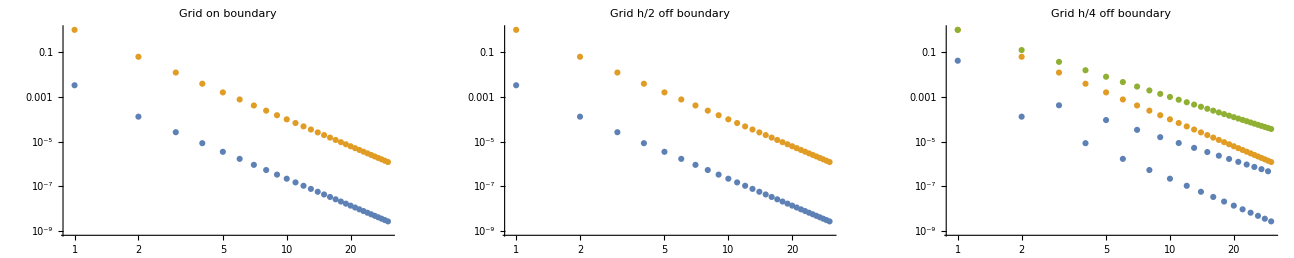

```mathematica
Show[
GraphicsGrid[
{
{ListLogLogPlot[
{Table[Abs[Re[f2hatθ[k]]] /. g1-> 1 /. g0-> 0.9 /. g2-> 1.2 /. x0-> 0.6 /. x2-> 0 /. θ->0 /. n-> 4,{k,1,30}],
Table[1/k^4,{k,1,30}]},PlotLabel->"Grid on boundary"],
ListLogLogPlot[
{Table[Abs[Re[f2hatθ[k]]] /. g1-> 1 /. g0-> 0.9 /. g2-> 1.2 /. x0-> 0.6 /. x2-> 0 /. θ->0.5 /. n-> 4,{k,1,30}],
Table[1/k^4,{k,1,30}]},PlotLabel->"Grid h/2 off boundary"],
ListLogLogPlot[
{Table[Abs[Re[f2hatθ[k]]] /. g1-> 1 /. g0-> 0.9 /. g2-> 1.2 /. x0-> 0.6 /. x2-> 0 /. θ->0.25 /. n-> 4,{k,1,30}],
Table[1/k^4,{k,1,30}],
Table[1/k^3,{k,1,30}]},PlotLabel->"Grid h/4 off boundary"]
}
}
]
]
```

### Final approximation comparison

Ansatz. Plot w.r.t n

```mathematica
FourierTransform[PDF[NormalDistribution[0,1/(√n)],z-y]PDF[NormalDistribution[0,1/(√n)],y-x],y,s,FourierParameters->{0, -2*Pi}]
```

(ⅇ^(-(π^2 s^2)/n-1/4 n (x-z)^2-ⅈ π s (x+z)) √n)/(2 √π)

```mathematica
Manipulate[
ListLogLogPlot[{
Table[2(3 n^3)/(2(π s)^4)Abs[(g2-2g1+g0)](g2-x2)(g0-x0)PDF[NormalDistribution[0,1/(√n)],g1 -x0]PDF[NormalDistribution[0,1/(√n)],g1 -x2]+√n ⅇ^(-(π^2 s^2)/n)ⅇ^(-n/4(x0-x2)^2)/.s-> k n^a ,{n,1,nmax}],
Table[
Abs[Re[1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π)/(2 √n)-(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π)/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π)/(2 √n)+(ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π)/(2 √n)-1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])/(2 √n))]]/.s-> k n^a /. θ-> 0,{n,1,nmax}]
}, PlotRange->Full,PlotLegends->{"ANSATZ","Real FT"}],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{k,1},1,20,1},{{a,0.75},0.5,1},{nmax,30,100},ContinuousAction->False]
```

Part::partd: Part specification Default.nb⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[Default.nb⟦2⟧,.nb→].

Part::partd: Part specification Default.nb⟦2⟧ is longer than depth of object.

StringReplace::strse: String or list of strings expected at position 1 in StringReplace[Default.nb⟦2⟧,.nb→].

```mathematica
Abs[Re[1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π)/(2 √n)-(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π)/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π)/(2 √n)+(ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π)/(2 √n)-1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])/(2 √n))]]/. s-> k n^a/. n-> 25 /. g0-> 1.3 /. g1 -> 1.38 /. g2 -> 3 /. x0 -> 0.5 /. x2 -> -1.3 /. k-> 1/.a -> 1
```

2.17796×10^-46

plot wrt n

```mathematica
Manipulate[
LogLogPlot[{
2(3 n^3)/(2(π s)^4)Abs[(g2-2g1+g0)] (g2-x2)(g0-x0)PDF[NormalDistribution[0,1/(√n)],g1 -x0]PDF[NormalDistribution[0,1/(√n)],g1 -x2]+√n ⅇ^(-(π^2 s^2)/n)ⅇ^(-n/4(x0-x2)^2)/.s-> k n^a ,

Abs[Re[1/(2 π)n ((ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π)/(2 √n)-(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π)/(2 √n)-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π)/(2 √n)+(ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π)/(2 √n)-1/(2 √n)ⅇ^(g0^2 n+g2^2 n+4 ⅈ (g0+g2) π s-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-ⅈ π s x2+(n x0 x2)/2-(n x2^2)/4-g0 (2 g1 n-2 g2 n+2 ⅈ π s+n x0+n x2)+2 g1 (-g2 n-ⅈ π s+n (x0+x2))-g2 (2 ⅈ π s+n (x0+x2))) √π Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-(ⅇ^(g2^2 n-(π^2 s^2)/n+2 ⅈ π s (2 g2+x0)+g2 (-2 ⅈ π s+n (x0-x2))-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2-2 g1 (g2 n+ⅈ π s-n x2)) √π Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(g0^2 n-(π^2 s^2)/n+2 g1 (-ⅈ π s+n x0)-g0 (2 g1 n+2 ⅈ π s+n (x0-x2))+2 ⅈ π s (2 g0+x2)-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √π Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)])/(2 √n)+(ⅇ^(-2 ⅈ g1 π s-(π^2 s^2)/n-1/4 n (x0-x2)^2+ⅈ π s (x0+x2)) √π Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])/(2 √n))]]/.s-> k n^a /. θ-> 0
},{n,1,50}, PlotRange->Full,PlotLegends->{"Vin bound","Real FT", "Bound"},PerformanceGoal->"Quality"],{{x0,0},-3,g0},{{x2,0},-3,g2},{{g0,0.6},0.5,3},{g1,0.5,3},{g2,0.5,3},{{k,1},1,20,1},{{a,0.75},0.5,1},ContinuousAction->False]
```

### Alternative Fourier method

```mathematica
f2[z_]:=(1-Exp[-2n(g2-x2)z])PDF[NormalDistribution[0,1/(√n)],g1 - z -x2](1-Exp[-2n(g0-x0)z ])PDF[NormalDistribution[0,1/(√n)],g1-z-x0]If[z>0,1,0]
```

```mathematica
D[f2[z],{z,4}]//Simplify
```

Piecewise[{{1/(2 π)ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2+12 g0 z+12 g2 z-10 x0 z-10 x2 z+2 z^2-2 g1 (x0+x2+2 z))) n^3 (ⅇ^(4 n (g0+g2-x0-x2) z) (12-48 g2^2 n+16 g0^4 n^2+16 g1^4 n^2+16 g2^4 n^2+48 g2 n x0-32 g2^3 n^2 x0-12 n x0^2+24 g2^2 n^2 x0^2-8 g2 n^2 x0^3+n^2 x0^4+48 g2 n x2-32 g2^3 n^2 x2-24 n x0 x2+48 g2^2 n^2 x0 x2-24 g2 n^2 x0^2 x2+4 n^2 x0^3 x2-12 n x2^2+24 g2^2 n^2 x2^2-24 g2 n^2 x0 x2^2+6 n^2 x0^2 x2^2-8 g2 n^2 x2^3+4 n^2 x0 x2^3+n^2 x2^4+24 g1^2 n (-2+4 g2^2 n-4 g2 n (x0+x2-2 z)+n (x0+x2-2 z)^2)-32 g0^3 n^2 (2 g1-2 g2+x0+x2-2 z)-96 g2 n z+64 g2^3 n^2 z+48 n x0 z-96 g2^2 n^2 x0 z+48 g2 n^2 x0^2 z-8 n^2 x0^3 z+48 n x2 z-96 g2^2 n^2 x2 z+96 g2 n^2 x0 x2 z-24 n^2 x0^2 x2 z+48 g2 n^2 x2^2 z-24 n^2 x0 x2^2 z-8 n^2 x2^3 z-48 n z^2+96 g2^2 n^2 z^2-96 g2 n^2 x0 z^2+24 n^2 x0^2 z^2-96 g2 n^2 x2 z^2+48 n^2 x0 x2 z^2+24 n^2 x2^2 z^2+64 g2 n^2 z^3-32 n^2 x0 z^3-32 n^2 x2 z^3+16 n^2 z^4-32 g1^3 n^2 (2 g2-x0-x2+2 z)-8 g1 n (-6+4 g2^2 n-4 g2 n (x0+x2-2 z)+n (x0+x2-2 z)^2) (2 g2-x0-x2+2 z)-8 g0 n (2 g1-2 g2+x0+x2-2 z) (-6+4 g1^2 n+4 g2^2 n+n x0^2+2 n x0 x2+n x2^2-4 g2 n (x0+x2-2 z)+4 g1 n (-2 g2+x0+x2-2 z)-4 n x0 z-4 n x2 z+4 n z^2)+24 g0^2 n (-2+4 g1^2 n+4 g2^2 n+n x0^2+2 n x0 x2+n x2^2-4 g2 n (x0+x2-2 z)+4 g1 n (-2 g2+x0+x2-2 z)-4 n x0 z-4 n x2 z+4 n z^2))-ⅇ^(2 n (3 g0+2 g2-3 x0-2 x2) z) (12+16 g1^4 n^2+16 g2^4 n^2-12 n x0^2+n^2 x0^4+24 n x0 x2-4 n^2 x0^3 x2-12 n x2^2+6 n^2 x0^2 x2^2-4 n^2 x0 x2^3+n^2 x2^4-48 n x0 z+8 n^2 x0^3 z+48 n x2 z-24 n^2 x0^2 x2 z+24 n^2 x0 x2^2 z-8 n^2 x2^3 z-48 n z^2+24 n^2 x0^2 z^2-48 n^2 x0 x2 z^2+24 n^2 x2^2 z^2+32 n^2 x0 z^3-32 n^2 x2 z^3+16 n^2 z^4+32 g2^3 n^2 (x0-x2+2 z)-32 g1^3 n^2 (2 g2+x0-x2+2 z)+8 g2 n (x0-x2+2 z) (-6+n (x0-x2+2 z)^2)+24 g2^2 n (-2+n (x0-x2+2 z)^2)-8 g1 n (2 g2+x0-x2+2 z) (-6+4 g2^2 n+4 g2 n (x0-x2+2 z)+n (x0-x2+2 z)^2)+24 g1^2 n (-2+4 g2^2 n+4 g2 n (x0-x2+2 z)+n (x0-x2+2 z)^2))-ⅇ^(2 n (2 g0+3 g2-2 x0-3 x2) z) (12+16 g0^4 n^2+16 g1^4 n^2-12 n x0^2+n^2 x0^4+24 n x0 x2-4 n^2 x0^3 x2-12 n x2^2+6 n^2 x0^2 x2^2-4 n^2 x0 x2^3+n^2 x2^4+32 g1^3 n^2 (x0-x2-2 z)-32 g0^3 n^2 (2 g1+x0-x2-2 z)+48 n x0 z-8 n^2 x0^3 z-48 n x2 z+24 n^2 x0^2 x2 z-24 n^2 x0 x2^2 z+8 n^2 x2^3 z-48 n z^2+24 n^2 x0^2 z^2-48 n^2 x0 x2 z^2+24 n^2 x2^2 z^2-32 n^2 x0 z^3+32 n^2 x2 z^3+16 n^2 z^4+8 g1 n (x0-x2-2 z) (-6+n (-x0+x2+2 z)^2)+24 g1^2 n (-2+n (-x0+x2+2 z)^2)-8 g0 n (2 g1+x0-x2-2 z) (-6+4 g1^2 n+4 g1 n (x0-x2-2 z)+n (-x0+x2+2 z)^2)+24 g0^2 n (-2+4 g1^2 n+4 g1 n (x0-x2-2 z)+n (-x0+x2+2 z)^2))+ⅇ^(6 n (g0+g2-x0-x2) z) (12+16 g1^4 n^2-32 g1^3 n^2 (x0+x2+2 z)-12 n (x0+x2+2 z)^2+n^2 (x0+x2+2 z)^4-8 g1 n (x0+x2+2 z) (-6+n (x0+x2+2 z)^2)+24 g1^2 n (-2+n (x0+x2+2 z)^2))), z>0}, {0, True}}]

#### F.T.

```mathematica
f2[z_]:=(1-Exp[-2n(g2-x2)z])PDF[NormalDistribution[0,1/(√n)],g1 - z -x2](1-Exp[-2n(g0-x0)z ])PDF[NormalDistribution[0,1/(√n)],g1-z-x0]If[z>0,1,0]
```

```mathematica
Evaluate[D[(1-Exp[-2n(g2-x2)z])PDF[NormalDistribution[0,1/(√n)],g1 - z -x2](1-Exp[-2n(g0-x0)z ])PDF[NormalDistribution[0,1/(√n)],g1-z-x0],{z,5}]]/.z-> 0//Simplify
```

(40 ⅇ^(-1/2 n ((g1-x0)^2+(g1-x2)^2)) (g0-2 g1+g2) n^5 (g0-x0) (-g2+x2) (-6+2 g0^2 n+4 g1^2 n-4 g1 g2 n+2 g2^2 n+n x0^2-2 g0 n (2 g1-g2+x0)-2 g2 n x2+n x2^2))/π

simplifying the polynomial stuff in the far right brackets

```mathematica
-6+2 g0^2 n+4 g1^2 n-4 g1 g2 n+2 g2^2 n+n x0^2-2 g0 n (2 g1-g2+x0)-2 g2 n x2+n x2^2 -(-6+n(g0-2 g1+g2)^2+n(g0-x0)^2+n(g2-x2)^2)//Simplify
```

0

```mathematica
D[f2[z],{z,4}]//Simplify
```

Piecewise[{{1/(2 π)ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2+12 g0 z+12 g2 z-10 x0 z-10 x2 z+2 z^2-2 g1 (x0+x2+2 z))) n^3 (ⅇ^(4 n (g0+g2-x0-x2) z) (12-48 g2^2 n+16 g0^4 n^2+16 g1^4 n^2+16 g2^4 n^2+48 g2 n x0-32 g2^3 n^2 x0-12 n x0^2+24 g2^2 n^2 x0^2-8 g2 n^2 x0^3+n^2 x0^4+48 g2 n x2-32 g2^3 n^2 x2-24 n x0 x2+48 g2^2 n^2 x0 x2-24 g2 n^2 x0^2 x2+4 n^2 x0^3 x2-12 n x2^2+24 g2^2 n^2 x2^2-24 g2 n^2 x0 x2^2+6 n^2 x0^2 x2^2-8 g2 n^2 x2^3+4 n^2 x0 x2^3+n^2 x2^4+24 g1^2 n (-2+4 g2^2 n-4 g2 n (x0+x2-2 z)+n (x0+x2-2 z)^2)-32 g0^3 n^2 (2 g1-2 g2+x0+x2-2 z)-96 g2 n z+64 g2^3 n^2 z+48 n x0 z-96 g2^2 n^2 x0 z+48 g2 n^2 x0^2 z-8 n^2 x0^3 z+48 n x2 z-96 g2^2 n^2 x2 z+96 g2 n^2 x0 x2 z-24 n^2 x0^2 x2 z+48 g2 n^2 x2^2 z-24 n^2 x0 x2^2 z-8 n^2 x2^3 z-48 n z^2+96 g2^2 n^2 z^2-96 g2 n^2 x0 z^2+24 n^2 x0^2 z^2-96 g2 n^2 x2 z^2+48 n^2 x0 x2 z^2+24 n^2 x2^2 z^2+64 g2 n^2 z^3-32 n^2 x0 z^3-32 n^2 x2 z^3+16 n^2 z^4-32 g1^3 n^2 (2 g2-x0-x2+2 z)-8 g1 n (-6+4 g2^2 n-4 g2 n (x0+x2-2 z)+n (x0+x2-2 z)^2) (2 g2-x0-x2+2 z)-8 g0 n (2 g1-2 g2+x0+x2-2 z) (-6+4 g1^2 n+4 g2^2 n+n x0^2+2 n x0 x2+n x2^2-4 g2 n (x0+x2-2 z)+4 g1 n (-2 g2+x0+x2-2 z)-4 n x0 z-4 n x2 z+4 n z^2)+24 g0^2 n (-2+4 g1^2 n+4 g2^2 n+n x0^2+2 n x0 x2+n x2^2-4 g2 n (x0+x2-2 z)+4 g1 n (-2 g2+x0+x2-2 z)-4 n x0 z-4 n x2 z+4 n z^2))-ⅇ^(2 n (3 g0+2 g2-3 x0-2 x2) z) (12+16 g1^4 n^2+16 g2^4 n^2-12 n x0^2+n^2 x0^4+24 n x0 x2-4 n^2 x0^3 x2-12 n x2^2+6 n^2 x0^2 x2^2-4 n^2 x0 x2^3+n^2 x2^4-48 n x0 z+8 n^2 x0^3 z+48 n x2 z-24 n^2 x0^2 x2 z+24 n^2 x0 x2^2 z-8 n^2 x2^3 z-48 n z^2+24 n^2 x0^2 z^2-48 n^2 x0 x2 z^2+24 n^2 x2^2 z^2+32 n^2 x0 z^3-32 n^2 x2 z^3+16 n^2 z^4+32 g2^3 n^2 (x0-x2+2 z)-32 g1^3 n^2 (2 g2+x0-x2+2 z)+8 g2 n (x0-x2+2 z) (-6+n (x0-x2+2 z)^2)+24 g2^2 n (-2+n (x0-x2+2 z)^2)-8 g1 n (2 g2+x0-x2+2 z) (-6+4 g2^2 n+4 g2 n (x0-x2+2 z)+n (x0-x2+2 z)^2)+24 g1^2 n (-2+4 g2^2 n+4 g2 n (x0-x2+2 z)+n (x0-x2+2 z)^2))-ⅇ^(2 n (2 g0+3 g2-2 x0-3 x2) z) (12+16 g0^4 n^2+16 g1^4 n^2-12 n x0^2+n^2 x0^4+24 n x0 x2-4 n^2 x0^3 x2-12 n x2^2+6 n^2 x0^2 x2^2-4 n^2 x0 x2^3+n^2 x2^4+32 g1^3 n^2 (x0-x2-2 z)-32 g0^3 n^2 (2 g1+x0-x2-2 z)+48 n x0 z-8 n^2 x0^3 z-48 n x2 z+24 n^2 x0^2 x2 z-24 n^2 x0 x2^2 z+8 n^2 x2^3 z-48 n z^2+24 n^2 x0^2 z^2-48 n^2 x0 x2 z^2+24 n^2 x2^2 z^2-32 n^2 x0 z^3+32 n^2 x2 z^3+16 n^2 z^4+8 g1 n (x0-x2-2 z) (-6+n (-x0+x2+2 z)^2)+24 g1^2 n (-2+n (-x0+x2+2 z)^2)-8 g0 n (2 g1+x0-x2-2 z) (-6+4 g1^2 n+4 g1 n (x0-x2-2 z)+n (-x0+x2+2 z)^2)+24 g0^2 n (-2+4 g1^2 n+4 g1 n (x0-x2-2 z)+n (-x0+x2+2 z)^2))+ⅇ^(6 n (g0+g2-x0-x2) z) (12+16 g1^4 n^2-32 g1^3 n^2 (x0+x2+2 z)-12 n (x0+x2+2 z)^2+n^2 (x0+x2+2 z)^4-8 g1 n (x0+x2+2 z) (-6+n (x0+x2+2 z)^2)+24 g1^2 n (-2+n (x0+x2+2 z)^2))), z>0}, {0, True}}]

```mathematica
FourierTransform[1/(2 π)ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2+12 g0 z+12 g2 z-10 x0 z-10 x2 z+2 z^2-2 g1 (x0+x2+2 z))) n^3 (ⅇ^(4 n (g0+g2-x0-x2) z) (12-48 g2^2 n+16 g0^4 n^2+16 g1^4 n^2+16 g2^4 n^2+48 g2 n x0-32 g2^3 n^2 x0-12 n x0^2+24 g2^2 n^2 x0^2-8 g2 n^2 x0^3+n^2 x0^4+48 g2 n x2-32 g2^3 n^2 x2-24 n x0 x2+48 g2^2 n^2 x0 x2-24 g2 n^2 x0^2 x2+4 n^2 x0^3 x2-12 n x2^2+24 g2^2 n^2 x2^2-24 g2 n^2 x0 x2^2+6 n^2 x0^2 x2^2-8 g2 n^2 x2^3+4 n^2 x0 x2^3+n^2 x2^4+24 g1^2 n (-2+4 g2^2 n-4 g2 n (x0+x2-2 z)+n (x0+x2-2 z)^2)-32 g0^3 n^2 (2 g1-2 g2+x0+x2-2 z)-96 g2 n z+64 g2^3 n^2 z+48 n x0 z-96 g2^2 n^2 x0 z+48 g2 n^2 x0^2 z-8 n^2 x0^3 z+48 n x2 z-96 g2^2 n^2 x2 z+96 g2 n^2 x0 x2 z-24 n^2 x0^2 x2 z+48 g2 n^2 x2^2 z-24 n^2 x0 x2^2 z-8 n^2 x2^3 z-48 n z^2+96 g2^2 n^2 z^2-96 g2 n^2 x0 z^2+24 n^2 x0^2 z^2-96 g2 n^2 x2 z^2+48 n^2 x0 x2 z^2+24 n^2 x2^2 z^2+64 g2 n^2 z^3-32 n^2 x0 z^3-32 n^2 x2 z^3+16 n^2 z^4-32 g1^3 n^2 (2 g2-x0-x2+2 z)-8 g1 n (-6+4 g2^2 n-4 g2 n (x0+x2-2 z)+n (x0+x2-2 z)^2) (2 g2-x0-x2+2 z)-8 g0 n (2 g1-2 g2+x0+x2-2 z) (-6+4 g1^2 n+4 g2^2 n+n x0^2+2 n x0 x2+n x2^2-4 g2 n (x0+x2-2 z)+4 g1 n (-2 g2+x0+x2-2 z)-4 n x0 z-4 n x2 z+4 n z^2)+24 g0^2 n (-2+4 g1^2 n+4 g2^2 n+n x0^2+2 n x0 x2+n x2^2-4 g2 n (x0+x2-2 z)+4 g1 n (-2 g2+x0+x2-2 z)-4 n x0 z-4 n x2 z+4 n z^2))-ⅇ^(2 n (3 g0+2 g2-3 x0-2 x2) z) (12+16 g1^4 n^2+16 g2^4 n^2-12 n x0^2+n^2 x0^4+24 n x0 x2-4 n^2 x0^3 x2-12 n x2^2+6 n^2 x0^2 x2^2-4 n^2 x0 x2^3+n^2 x2^4-48 n x0 z+8 n^2 x0^3 z+48 n x2 z-24 n^2 x0^2 x2 z+24 n^2 x0 x2^2 z-8 n^2 x2^3 z-48 n z^2+24 n^2 x0^2 z^2-48 n^2 x0 x2 z^2+24 n^2 x2^2 z^2+32 n^2 x0 z^3-32 n^2 x2 z^3+16 n^2 z^4+32 g2^3 n^2 (x0-x2+2 z)-32 g1^3 n^2 (2 g2+x0-x2+2 z)+8 g2 n (x0-x2+2 z) (-6+n (x0-x2+2 z)^2)+24 g2^2 n (-2+n (x0-x2+2 z)^2)-8 g1 n (2 g2+x0-x2+2 z) (-6+4 g2^2 n+4 g2 n (x0-x2+2 z)+n (x0-x2+2 z)^2)+24 g1^2 n (-2+4 g2^2 n+4 g2 n (x0-x2+2 z)+n (x0-x2+2 z)^2))-ⅇ^(2 n (2 g0+3 g2-2 x0-3 x2) z) (12+16 g0^4 n^2+16 g1^4 n^2-12 n x0^2+n^2 x0^4+24 n x0 x2-4 n^2 x0^3 x2-12 n x2^2+6 n^2 x0^2 x2^2-4 n^2 x0 x2^3+n^2 x2^4+32 g1^3 n^2 (x0-x2-2 z)-32 g0^3 n^2 (2 g1+x0-x2-2 z)+48 n x0 z-8 n^2 x0^3 z-48 n x2 z+24 n^2 x0^2 x2 z-24 n^2 x0 x2^2 z+8 n^2 x2^3 z-48 n z^2+24 n^2 x0^2 z^2-48 n^2 x0 x2 z^2+24 n^2 x2^2 z^2-32 n^2 x0 z^3+32 n^2 x2 z^3+16 n^2 z^4+8 g1 n (x0-x2-2 z) (-6+n (-x0+x2+2 z)^2)+24 g1^2 n (-2+n (-x0+x2+2 z)^2)-8 g0 n (2 g1+x0-x2-2 z) (-6+4 g1^2 n+4 g1 n (x0-x2-2 z)+n (-x0+x2+2 z)^2)+24 g0^2 n (-2+4 g1^2 n+4 g1 n (x0-x2-2 z)+n (-x0+x2+2 z)^2))+ⅇ^(6 n (g0+g2-x0-x2) z) (12+16 g1^4 n^2-32 g1^3 n^2 (x0+x2+2 z)-12 n (x0+x2+2 z)^2+n^2 (x0+x2+2 z)^4-8 g1 n (x0+x2+2 z) (-6+n (x0+x2+2 z)^2)+24 g1^2 n (-2+n (x0+x2+2 z)^2)))If[z>0,1,0],z,s,FourierParameters->{0, -2*Pi}]
```

1/π 4 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) √n (3 g0^2 g2 n^(7/2)-6 g0 g1 g2 n^(7/2)+3 g0 g2^2 n^(7/2)-2 ⅈ g0 g2 n^(5/2) π s-ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n)) π^(9/2) s^4-ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n)) π^(9/2) s^4-3 g0 g2 n^(7/2) x0+6 g1 g2 n^(7/2) x0-3 g2^2 n^(7/2) x0+2 ⅈ g2 n^(5/2) π s x0-3 g0^2 n^(7/2) x2+6 g0 g1 n^(7/2) x2-3 g0 g2 n^(7/2) x2+2 ⅈ g0 n^(5/2) π s x2+3 g0 n^(7/2) x0 x2-6 g1 n^(7/2) x0 x2+3 g2 n^(7/2) x0 x2-2 ⅈ n^(5/2) π s x0 x2-ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]+ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n)) π^(9/2) s^4 Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])

```mathematica
1/π 4 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) √n (3 g0^2 g2 n^(7/2)-6 g0 g1 g2 n^(7/2)+3 g0 g2^2 n^(7/2)-2 ⅈ g0 g2 n^(5/2) π s-ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n)) π^(9/2) s^4-ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n)) π^(9/2) s^4-3 g0 g2 n^(7/2) x0+6 g1 g2 n^(7/2) x0-3 g2^2 n^(7/2) x0+2 ⅈ g2 n^(5/2) π s x0-3 g0^2 n^(7/2) x2+6 g0 g1 n^(7/2) x2-3 g0 g2 n^(7/2) x2+2 ⅈ g0 n^(5/2) π s x2+3 g0 n^(7/2) x0 x2-6 g1 n^(7/2) x0 x2+3 g2 n^(7/2) x0 x2-2 ⅈ n^(5/2) π s x0 x2-ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]+ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n)) π^(9/2) s^4 Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])//FullSimplify
```

$Aborted

```mathematica
3 g0^2 g2 n^(7/2)-6 g0 g1 g2 n^(7/2)+3 g0 g2^2 n^(7/2)-2 ⅈ g0 g2 n^(5/2) π s-3 g0 g2 n^(7/2) x0+6 g1 g2 n^(7/2) x0-3 g2^2 n^(7/2) x0+2 ⅈ g2 n^(5/2) π s x0-3 g0^2 n^(7/2) x2+6 g0 g1 n^(7/2) x2-3 g0 g2 n^(7/2) x2+2 ⅈ g0 n^(5/2) π s x2+3 g0 n^(7/2) x0 x2-6 g1 n^(7/2) x0 x2+3 g2 n^(7/2) x0 x2-2 ⅈ n^(5/2) π s x0 x2//Simplify
```

n^(5/2) (3 g0 n-6 g1 n+3 g2 n-2 ⅈ π s) (g0-x0) (g2-x2)

```mathematica
Simplify[ComplexExpand[Re[n^(5/2) (3 g0 n-6 g1 n+3 g2 n-2 ⅈ π s) (g0-x0) (g2-x2)]],n>0]
```

3 (g0-2 g1+g2) n^(7/2) (g0-x0) (g2-x2)

```mathematica
Simplify[ComplexExpand[Im[n^(5/2) (3 g0 n-6 g1 n+3 g2 n-2 ⅈ π s) (g0-x0) (g2-x2)]],n>0]
```

-2 n^(5/2) π s (g0-x0) (g2-x2)

```mathematica
Abs[-ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n)) π^(9/2) s^4-ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n)) π^(9/2) s^4] //Simplify
```

π^(9/2) Abs[(ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n))+ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n))-ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n))-ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n))) s^4]

```mathematica
Manipulate[LogLogPlot[{
Abs[-ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n)) π^(9/2) s^4-ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n)) π^(9/2) s^4] ,
10^-3/s},{s,1,50}, PlotLegends-> {"Tail FT (Abs)","Tail FT (Real)","1/s"},PlotStyle->{Opacity[a],Dashed}],{g0,0.5,2},{g1,0.5,2},{g2,0.5,2},{n,1,10},{x0,-3,g0},{x2,-3,g2},{{a,0.7},0,1},ControlPlacement->Left]
```

```mathematica
m1:=ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n))
m2:=ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n))
m3:=ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n))
m4:=ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n))
z1:=(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)
z2:=(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)
z3:=(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)
z4:=(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)
```

```mathematica
Series[Erf[z],{z,∞,2}]
```

1+ⅇ^(-z^2) (-1/(√π z)+O[1/z]^3)

```mathematica
{m1 ⅇ^(-z1^2),m2 ⅇ^(-z2^2),m3 ⅇ^(-z3^2),m4 ⅇ^(-z4^2)}//Simplify
```

{1,1,1,1}

```mathematica
π^(9/2) s^4  Series[Simplify[Im[-1/z1-1/z2+1/z3+1/z4],n>0],{s,∞,5}]//Simplify
```

-2 (n^(5/2) π^(3/2) (g0-x0) (g2-x2)) s+(n^(9/2) (g0-x0) (g2-x2) (4 g0^2+12 g1^2-12 g1 g2+4 g2^2+x0^2-2 g0 (6 g1-3 g2+x0)-2 g2 x2+x2^2))/(√π s)+O[1/s]^2

```mathematica
π^(9/2) s^4  Series[Simplify[Re[-1/z1-1/z2+1/z3+1/z4],n>0],{s,∞,4}]//Simplify
```

3 (g0-2 g1+g2) n^(7/2) √π (g0-x0) (g2-x2)+O[1/s]^1

an extra s pops out...

```mathematica
π^(9/2) s^4  Series[Simplify[ComplexExpand[1/Abs[z1^3]+1/Abs[z2^3]+1/Abs[z3^3]+1/Abs[z4^3]],n>0],{s,∞,4}]//Simplify
```

4 n^(3/2) π^(3/2) s+O[1/s]^1

```mathematica
π^(9/2) s^4  Series[Simplify[Re[-1/z1^3-1/z2^3+1/z3^3+1/z4^3],n>0],{s,∞,8}]//Simplify
```

-(30 ((g0-2 g1+g2) n^(9/2) (g0-x0) (g2-x2)))/(π^(3/2) s^2)+(105 (g0-2 g1+g2) n^(13/2) (g0-x0) (g2-x2) (2 g0^2+4 g1^2-4 g1 g2+2 g2^2+x0^2-2 g0 (2 g1-g2+x0)-2 g2 x2+x2^2))/(2 π^(7/2) s^4)+O[1/s]^5

```mathematica
π^(9/2) s^4  Series[Simplify[Im[-1/z1^3-1/z2^3+1/z3^3+1/z4^3],n>0],{s,∞,6}]//Simplify
```

(12 n^(7/2) (g0-x0) (g2-x2))/(√π s)+O[1/s]^3

#### F.T. simplification

Conv. rate disagree when for Real vs Abs when g is vastly different from g2

```mathematica
Manipulate[LogLogPlot[{
Abs[1/π 4 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) √n (3 g0^2 g2 n^(7/2)-6 g0 g1 g2 n^(7/2)+3 g0 g2^2 n^(7/2)-2 ⅈ g0 g2 n^(5/2) π s-ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n)) π^(9/2) s^4-ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n)) π^(9/2) s^4-3 g0 g2 n^(7/2) x0+6 g1 g2 n^(7/2) x0-3 g2^2 n^(7/2) x0+2 ⅈ g2 n^(5/2) π s x0-3 g0^2 n^(7/2) x2+6 g0 g1 n^(7/2) x2-3 g0 g2 n^(7/2) x2+2 ⅈ g0 n^(5/2) π s x2+3 g0 n^(7/2) x0 x2-6 g1 n^(7/2) x0 x2+3 g2 n^(7/2) x0 x2-2 ⅈ n^(5/2) π s x0 x2-ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]+ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n)) π^(9/2) s^4 Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])],
Abs[Re[1/π 4 ⅇ^(-1/2 n (2 g1^2+x0^2+x2^2-2 g1 (x0+x2))) √n (3 g0^2 g2 n^(7/2)-6 g0 g1 g2 n^(7/2)+3 g0 g2^2 n^(7/2)-2 ⅈ g0 g2 n^(5/2) π s-ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n)) π^(9/2) s^4-ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n)) π^(9/2) s^4+ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n)) π^(9/2) s^4-3 g0 g2 n^(7/2) x0+6 g1 g2 n^(7/2) x0-3 g2^2 n^(7/2) x0+2 ⅈ g2 n^(5/2) π s x0-3 g0^2 n^(7/2) x2+6 g0 g1 n^(7/2) x2-3 g0 g2 n^(7/2) x2+2 ⅈ g0 n^(5/2) π s x2+3 g0 n^(7/2) x0 x2-6 g1 n^(7/2) x0 x2+3 g2 n^(7/2) x0 x2-2 ⅈ n^(5/2) π s x0 x2-ⅇ^((-2 g0 n+2 g1 n-2 g2 n-2 ⅈ π s+n x0+n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g0 n-2 g1 n+2 g2 n+2 ⅈ π s-n x0-n x2)/(2 √n)]-ⅇ^((-2 g1 n+2 g2 n+2 ⅈ π s+n x0-n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g1 n-2 g2 n-2 ⅈ π s-n x0+n x2)/(2 √n)]+ⅇ^((2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)^2/(4 n)) π^(9/2) s^4 Erf[(2 g0 n-2 g1 n+2 ⅈ π s-n x0+n x2)/(2 √n)]+ⅇ^((-2 g1 n+2 ⅈ π s+n (x0+x2))^2/(4 n)) π^(9/2) s^4 Erf[(2 g1 n-2 ⅈ π s-n (x0+x2))/(2 √n)])]],
10^-3/s},{s,1,50}, PlotLegends-> {"Tail FT (Abs)","Tail FT (Real)","1/s"},PlotStyle->{Opacity[a],Dashed}],{g0,0.5,2},{g1,0.5,2},{g2,0.5,2},{n,1,10},{x0,-3,g0},{x2,-3,g2},{{a,0.7},0,1},ControlPlacement->Left]
```

## Exponential convergence for linear boundaries

### Fourier transform

Centering function for Fourier transforms at the boundary and changing to parameter to express the distance from the boundary

```mathematica
f4[y_]:=(1 - Exp[-2 n(g+Kc/n-x2)(g-y)])PDF[NormalDistribution[0,1/(√n)],x2-y]*(1 - Exp[-2 n(g-y)(g - Kc/n-x0)])PDF[NormalDistribution[0,1/(√n)],x0-y]
```

```mathematica
f4e[y_]=f4[g-y]
```

(ⅇ^(-1/2 n (-g+x0+y)^2-1/2 n (-g+x2+y)^2) (1-ⅇ^(-2 n (g-Kc/n-x0) y)) (1-ⅇ^(-2 n (g+Kc/n-x2) y)) n)/(2 π)

```mathematica
(ⅇ^(-1/2 n (-g+x0+y)^2-1/2 n (-g+x2+y)^2) (1-ⅇ^(-2 n (g-Kc/n-x0) y)) (1-ⅇ^(-2 n (g+Kc/n-x2) y)) n)/(2 π) /.y-> -y
```

(ⅇ^(-1/2 n (-g+x0-y)^2-1/2 n (-g+x2-y)^2) (1-ⅇ^(2 n (g-Kc/n-x0) y)) (1-ⅇ^(2 n (g+Kc/n-x2) y)) n)/(2 π)

```mathematica
(ⅇ^(-1/2 n (-g+x0+y)^2-1/2 n (-g+x2+y)^2) (1-ⅇ^(-2 n (g-Kc/n-x0) y)) (1-ⅇ^(-2 n (g+Kc/n-x2) y)) n)/(2 π) -(ⅇ^(-1/2 n (-g+x0-y)^2-1/2 n (-g+x2-y)^2) (1-ⅇ^(2 n (g-Kc/n-x0) y)) (1-ⅇ^(2 n (g+Kc/n-x2) y)) n)/(2 π)//Simplify
```

0

```mathematica
(ⅇ^(-1/2 n (-g+x0+y)^2-1/2 n (-g+x2+y)^2) (1-ⅇ^(-2 n (g-Kc/n-x0) y)) (1-ⅇ^(-2 n (g+Kc/n-x2) y)) n)/(2 π) /. y-> y + δ/n
```

(ⅇ^(-1/2 n (-g+x0+y+δ/n)^2-1/2 n (-g+x2+y+δ/n)^2) (1-ⅇ^(-2 n (g-Kc/n-x0) (y+δ/n))) (1-ⅇ^(-2 n (g+Kc/n-x2) (y+δ/n))) n)/(2 π)

```mathematica
Manipulate[Plot[{(ⅇ^(-1/2 n (-g+x0+y)^2-1/2 n (-g+x2+y)^2) (1-ⅇ^(-2 n (g-Kc/n-x0) y)) (1-ⅇ^(-2 n (g+Kc/n-x2) y)) n)/(2 π),(ⅇ^(-1/2 n (-g+x0+y+δ/n)^2-1/2 n (-g+x2+y+δ/n)^2) (1-ⅇ^(-2 n (g-Kc/n-x0) (y+δ/n))) (1-ⅇ^(-2 n (g+Kc/n-x2) (y+δ/n))) n)/(2 π)},{y,-6,6},PlotRange->Full],{δ,0,1},{x0,-3,g-Kc/n},{x2,-3,g+Kc/n},{n,2,40,1},{g,1/3,2},{Kc,-1,1},ControlPlacement->Left]
```

```mathematica
Manipulate[Plot[{Abs[(ⅇ^(-1/2 n (-g+x0+y)^2-1/2 n (-g+x2+y)^2) (1-ⅇ^(-2 n (g-Kc/n-x0) y)) (1-ⅇ^(-2 n (g+Kc/n-x2) y)) n)/(2 π)-(ⅇ^(-1/2 n (-g+x0+y+δ/n)^2-1/2 n (-g+x2+y+δ/n)^2) (1-ⅇ^(-2 n (g-Kc/n-x0) (y+δ/n))) (1-ⅇ^(-2 n (g+Kc/n-x2) (y+δ/n))) n)/(2 π)]},{y,-6,6},PlotRange->Full],{{δ,0.3},0,1},{x0,-3,g-Kc/n},{x2,-3,g+Kc/n},{n,2,100,1},{g,0.5,2},{{Kc,0.2},-1,1},ControlPlacement->Left]
```

Fourier transform has no Error functions as expected. Since the original function is symmetric, the Fourier transform is real valued

```mathematica
Assuming[h >0 &&n>0 &&g>0 && Element[h, Reals]&& Element[Kc, Reals] && Element[g, Reals]&& Element[x0, Reals]&& Element[x2, Reals] && Element[n, Reals],FourierTransform[f4e[t],t,s,FourierParameters->{0,-2Pi}]]
```

1/(2 √π)ⅇ^(-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) (-ⅇ^((2 Kc-2 ⅈ π s+n x0-n x2)^2/(4 n))-ⅇ^((2 Kc+2 ⅈ π s+n x0-n x2)^2/(4 n))+ⅇ^((2 g n+2 ⅈ π s-n (x0+x2))^2/(4 n))+ⅇ^((-2 g n+2 ⅈ π s+n (x0+x2))^2/(4 n))) √n

Simplified FT in terms of trig functions

```mathematica
1/(2 √π)ⅇ^(-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) (ⅇ^(-(π^2 s^2)/n) (-2 ⅇ^((2 Kc+n (x0-x2))^2/(4 n)) Cos[(π s (2 Kc+n (x0-x2)))/n]+2 ⅇ^(1/4 n (-2 g+x0+x2)^2) Cos[π s (2 g-x0-x2)])) √n//FullSimplify
```

1/(√π)ⅇ^(-(π^2 s^2)/n-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) √n (-ⅇ^((2 Kc+n (x0-x2))^2/(4 n)) Cos[(π s (2 Kc+n (x0-x2)))/n]+ⅇ^(1/4 n (-2 g+x0+x2)^2) Cos[π s (2 g-x0-x2)])

```mathematica
1/(√π)ⅇ^(-(π^2 s^2)/n-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) √n (-ⅇ^((2 Kc+n (x0-x2))^2/(4 n)) Cos[(π s (2 Kc+n (x0-x2)))/n]+ⅇ^(1/4 n (-2 g+x0+x2)^2) Cos[π s (2 g-x0-x2)]) /. s -> k n^a
```

1/(√π)ⅇ^(-k^2 n^(-1+2 a) π^2-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) √n (-ⅇ^((2 Kc+n (x0-x2))^2/(4 n)) Cos[k n^(-1+a) π (2 Kc+n (x0-x2))]+ⅇ^(1/4 n (-2 g+x0+x2)^2) Cos[k n^a π (2 g-x0-x2)])

```mathematica
Manipulate[ListLogLogPlot[{
Table[Abs[1/(√π)ⅇ^(-k^2 n^(-1+2 a) π^2-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) √n (-ⅇ^((2 Kc+n (x0-x2))^2/(4 n)) Cos[k n^(-1+a) π (2 Kc+n (x0-x2))]+ⅇ^(1/4 n (-2 g+x0+x2)^2) Cos[k n^a π (2 g-x0-x2)])],{n,1,200}],
Table[(ⅇ^(-k^2 n^(-1+2 a) π^2-1/2 n (2 g^2+x0^2+x2^2-2 g (x0+x2))) √n (ⅇ^((2 Kc+n (x0-x2))^2/(4 n)) +ⅇ^(1/4 n (-2 g+x0+x2)^2) ))/(√π),{n,1,200}],
Table[Abs[(ⅇ^(-k^2 n^(-1+2 a) π^2) (ⅇ^(Kc^2/n)+1) √n)/(√π)],{n,1,200}],
Table[Abs[1/n^4],{n,1,100}]
},PlotLegends->{"Abs","Upper bound", "parameter indept. upper bound","1/n^4"}],{{x0,0},-3,g -Kc},{{x2,0},-3,g+Kc},{{g,0.6},0.5,3},{{k,1},1,5,1},{Kc,0,1},{{a,0.75},0.5,1},ControlPlacement->Left]
```

```mathematica
(g - Kc/n-x0 )(ⅇ^(-n/2(g - x0)^2) √n (ⅇ^((2 Kc+n (x0-x2))^2/(4 n)) +ⅇ^(1/4 n (-2 g+x0+x2)^2) ))/(√π)PDF[NormalDistribution[0,√((k-1)/n)],x0]
```

```mathematica
∫_(-∞)^(g-Kc/n) (g - Kc/n-x0 ) ⅇ^(-n/2(g - x0)^2) PDF[NormalDistribution[0,√((k-1)/n)],x0] ⅇ^((2 Kc+n (x0-x2))^2/(4 n))ⅆx0
```

ConditionalExpression[1/(√((-1+k)/n) √(2 π))ⅇ^(Kc^2/n-(g^2 n)/2-Kc x2+(n x2^2)/4) ((ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) g √π)/(√(((1+k) n)/(-1+k)))-(ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) Kc √π)/(n √(((1+k) n)/(-1+k)))-(ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) √π (2 Kc+2 g n-n x2))/(((1+k) n)/(-1+k))^(3/2)+(2 (-1+k) (1+(ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) √(-1+k) √π (2 Kc+2 g n-n x2) Erf[(√(-1+k) Kc)/(√(1+k) √n)+(g √(-1+k) √n)/(√(1+k))-(√(-1+k) √n x2)/(2 √(1+k))])/(2 √(1+k) √n)))/((1+k) n)+1/((1+k) n^2)(-1+k) Kc (2 Kc+2 g n-n x2) (1+1/((-1+k) (2 Kc+2 g n-n x2)^2)(4 Kc^2-4 k Kc^2+8 g Kc n-8 g k Kc n+4 g^2 n^2-4 g^2 k n^2-4 Kc n x2+4 k Kc n x2-4 g n^2 x2+4 g k n^2 x2+n^2 x2^2-k n^2 x2^2+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) k n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]))-1/((1+k) n)g (-1+k) (2 Kc+2 g n-n x2) (1+1/((-1+k) (2 Kc+2 g n-n x2)^2)(4 Kc^2-4 k Kc^2+8 g Kc n-8 g k Kc n+4 g^2 n^2-4 g^2 k n^2-4 Kc n x2+4 k Kc n x2-4 g n^2 x2+4 g k n^2 x2+n^2 x2^2-k n^2 x2^2+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) k n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]))+1/(√(((1+k) n)/(-1+k)))2 ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) (-(-1+ⅇ^(-((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)))/(√(((1+k) n)/(-1+k)))+(-1+ⅇ^(-((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/(4 (-1+k) (1+k) n)))/(√(((1+k) n)/(-1+k)))-(k Kc √π (2 Kc+2 g n-n x2) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((-1+k) (((1+k) n)/(-1+k))^(3/2) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(g k √π (2 Kc+2 g n-n x2) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(Kc √π (2 Kc+2 g n-n x2) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 n √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(Kc √π (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((-1+k) (((1+k) n)/(-1+k))^(3/2) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(g √π (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(g √π (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))+(√π x2 (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 (1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(k √π x2 (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 (1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))+(k √π x2 (Kc-3 k Kc-n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 (-1+k^2) √(((1+k) n)/(-1+k)) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))-(Kc √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/((-1+k)^2 (((1+k) n)/(-1+k))^(3/2) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))+(k Kc √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/((-1+k)^2 (((1+k) n)/(-1+k))^(3/2) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))+((1+k) Kc √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 (-1+k)^2 (((1+k) n)/(-1+k))^(3/2) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))-(g √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 (-1+k) √(((1+k) n)/(-1+k)) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))-(g n √π √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(√(((1+k) n)/(-1+k)) ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)))+(g k n √π √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(√(((1+k) n)/(-1+k)) ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)))+(n √π x2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 √(((1+k) n)/(-1+k)) ((-1+3 k) Kc+n (g (-3+k)+x2-k x2))))),(Re[((1+k) n)/(-1+k)]==0&&Re[(n+k n)/(1-k)]≤0&&Re[2 Kc+2 g n-n x2]<0&&Re[-2 Kc+n (-2 g+x2)]<0)||Re[(n+k n)/(1-k)]<0]

```mathematica
μ1[g_,n_,x2_,Kc_,k_]:=ⅇ^(-n/2(g - x2)^2)(1/(√((-1+k)/n) √(2 π))ⅇ^(Kc^2/n-(g^2 n)/2-Kc x2+(n x2^2)/4) ((ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) g √π)/(√(((1+k) n)/(-1+k)))-(ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) Kc √π)/(n √(((1+k) n)/(-1+k)))-(ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) √π (2 Kc+2 g n-n x2))/(((1+k) n)/(-1+k))^(3/2)+(2 (-1+k) (1+(ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) √(-1+k) √π (2 Kc+2 g n-n x2) Erf[(√(-1+k) Kc)/(√(1+k) √n)+(g √(-1+k) √n)/(√(1+k))-(√(-1+k) √n x2)/(2 √(1+k))])/(2 √(1+k) √n)))/((1+k) n)+1/((1+k) n^2)(-1+k) Kc (2 Kc+2 g n-n x2) (1+1/((-1+k) (2 Kc+2 g n-n x2)^2)(4 Kc^2-4 k Kc^2+8 g Kc n-8 g k Kc n+4 g^2 n^2-4 g^2 k n^2-4 Kc n x2+4 k Kc n x2-4 g n^2 x2+4 g k n^2 x2+n^2 x2^2-k n^2 x2^2+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) k n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]))-1/((1+k) n)g (-1+k) (2 Kc+2 g n-n x2) (1+1/((-1+k) (2 Kc+2 g n-n x2)^2)(4 Kc^2-4 k Kc^2+8 g Kc n-8 g k Kc n+4 g^2 n^2-4 g^2 k n^2-4 Kc n x2+4 k Kc n x2-4 g n^2 x2+4 g k n^2 x2+n^2 x2^2-k n^2 x2^2+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) k n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]))+1/(√(((1+k) n)/(-1+k)))2 ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) (-(-1+ⅇ^(-((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)))/(√(((1+k) n)/(-1+k)))+(-1+ⅇ^(-((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/(4 (-1+k) (1+k) n)))/(√(((1+k) n)/(-1+k)))-(k Kc √π (2 Kc+2 g n-n x2) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((-1+k) (((1+k) n)/(-1+k))^(3/2) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(g k √π (2 Kc+2 g n-n x2) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(Kc √π (2 Kc+2 g n-n x2) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 n √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(Kc √π (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((-1+k) (((1+k) n)/(-1+k))^(3/2) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(g √π (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(g √π (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))+(√π x2 (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 (1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(k √π x2 (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 (1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))+(k √π x2 (Kc-3 k Kc-n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 (-1+k^2) √(((1+k) n)/(-1+k)) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))-(Kc √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/((-1+k)^2 (((1+k) n)/(-1+k))^(3/2) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))+(k Kc √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/((-1+k)^2 (((1+k) n)/(-1+k))^(3/2) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))+((1+k) Kc √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 (-1+k)^2 (((1+k) n)/(-1+k))^(3/2) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))-(g √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 (-1+k) √(((1+k) n)/(-1+k)) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))-(g n √π √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(√(((1+k) n)/(-1+k)) ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)))+(g k n √π √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(√(((1+k) n)/(-1+k)) ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)))+(n √π x2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 √(((1+k) n)/(-1+k)) ((-1+3 k) Kc+n (g (-3+k)+x2-k x2))))))
```

```mathematica
Assuming[g>0 && n>1 && k >1,∫_(-∞)^(g-Kc/n) (g - Kc/n-x0 ) ⅇ^(-n/2(g - x0)^2) PDF[NormalDistribution[0,√((k-1)/n)],x0] ⅇ^(1/4 n (-2 g+x0+x2)^2) ⅆx0]
```

-1/n ⅇ^((g^2 n)/2-g n x2+(n x2^2)/4) √(-n/(2 π-2 k π)) (-(2 (-1+k))/(1+k)-√((-1+k)/((1+k) n)) (-Kc+g n) √π-((-1+k) Kc x2)/(1+k)+(g (-1+k) n x2)/(1+k)+((((-1+k) n)/(1+k))^(3/2) √π x2)/n+((-1+ⅇ^(((-1+k) n x2^2)/(4 (1+k)))) (((-1+k) n)/(1+k))^(3/2) √π x2)/n-1/(1+k)^(3/2)√π (Kc √((-1+k)/n)-ⅇ^(((-1+k) n x2^2)/(4 (1+k))) Kc √((-1+k)/n)+k Kc √((-1+k)/n)-ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k Kc √((-1+k)/n)-g √((-1+k)/n) n+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) g √((-1+k)/n) n-g k √((-1+k)/n) n+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) g k √((-1+k)/n) n-ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √((-1+k) n) x2 Erf[1/2 √(((-1+k) n)/(1+k)) x2]+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k √((-1+k) n) x2 Erf[1/2 √(((-1+k) n)/(1+k)) x2])+(g (n x2^2-k n x2^2+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)]+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)]))/((1+k) x2)-(Kc (n x2^2-k n x2^2+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)]+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)]))/((1+k) n x2)+2 ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √((-1+k)/((1+k) n)) (-ⅇ^(-((-1+k) n x2^2)/(4 (1+k))) (-1+ⅇ^(((-1+k) n x2^2)/(4 (1+k)))) √((-1+k)/((1+k) n)) n-((-1+ⅇ^(-((-g √((1+k)/(-1+k)) n^(3/2)+Kc √(((1+k) n)/(-1+k))+√((-1+k)/(1+k)) n^(3/2) x2)^2)/(4 n^2))) √((-1+k^2) n))/(1+k)+(Kc √π x2 Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 √(x2^2))-(g n √π x2 Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 √(x2^2))-(n √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 (1+k))+(k n √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 (1+k))+(Kc √((-1+k^2) n) √π ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 √(((1+k) Kc-n (g+g k+x2-k x2))^2))-(g n √((-1+k^2) n) √π ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 √(((1+k) Kc-n (g+g k+x2-k x2))^2))-(n √((-1+k^2) n) √π x2 ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 (1+k) √(((1+k) Kc-n (g+g k+x2-k x2))^2))+(k n √((-1+k^2) n) √π x2 ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 (1+k) √(((1+k) Kc-n (g+g k+x2-k x2))^2))))

```mathematica
μ2[g_,n_,x2_,Kc_,k_]:=ⅇ^(-n/2(g - x2)^2)(-1/n ⅇ^((g^2 n)/2-g n x2+(n x2^2)/4) √(-n/(2 π-2 k π)) (-(2 (-1+k))/(1+k)-√((-1+k)/((1+k) n)) (-Kc+g n) √π-((-1+k) Kc x2)/(1+k)+(g (-1+k) n x2)/(1+k)+((((-1+k) n)/(1+k))^(3/2) √π x2)/n+((-1+ⅇ^(((-1+k) n x2^2)/(4 (1+k)))) (((-1+k) n)/(1+k))^(3/2) √π x2)/n-1/(1+k)^(3/2)√π (Kc √((-1+k)/n)-ⅇ^(((-1+k) n x2^2)/(4 (1+k))) Kc √((-1+k)/n)+k Kc √((-1+k)/n)-ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k Kc √((-1+k)/n)-g √((-1+k)/n) n+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) g √((-1+k)/n) n-g k √((-1+k)/n) n+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) g k √((-1+k)/n) n-ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √((-1+k) n) x2 Erf[1/2 √(((-1+k) n)/(1+k)) x2]+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k √((-1+k) n) x2 Erf[1/2 √(((-1+k) n)/(1+k)) x2])+(g (n x2^2-k n x2^2+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)]+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)]))/((1+k) x2)-(Kc (n x2^2-k n x2^2+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)]+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)]))/((1+k) n x2)+2 ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √((-1+k)/((1+k) n)) (-ⅇ^(-((-1+k) n x2^2)/(4 (1+k))) (-1+ⅇ^(((-1+k) n x2^2)/(4 (1+k)))) √((-1+k)/((1+k) n)) n-((-1+ⅇ^(-((-g √((1+k)/(-1+k)) n^(3/2)+Kc √(((1+k) n)/(-1+k))+√((-1+k)/(1+k)) n^(3/2) x2)^2)/(4 n^2))) √((-1+k^2) n))/(1+k)+(Kc √π x2 Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 √(x2^2))-(g n √π x2 Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 √(x2^2))-(n √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 (1+k))+(k n √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 (1+k))+(Kc √((-1+k^2) n) √π ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 √(((1+k) Kc-n (g+g k+x2-k x2))^2))-(g n √((-1+k^2) n) √π ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 √(((1+k) Kc-n (g+g k+x2-k x2))^2))-(n √((-1+k^2) n) √π x2 ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 (1+k) √(((1+k) Kc-n (g+g k+x2-k x2))^2))+(k n √((-1+k^2) n) √π x2 ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 (1+k) √(((1+k) Kc-n (g+g k+x2-k x2))^2)))))
```

```mathematica
μ[g_,n_,x2_,Kc_,k_]:=ⅇ^(-n/2(g - x2)^2)(1/(√((-1+k)/n) √(2 π))ⅇ^(Kc^2/n-(g^2 n)/2-Kc x2+(n x2^2)/4) ((ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) g √π)/(√(((1+k) n)/(-1+k)))-(ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) Kc √π)/(n √(((1+k) n)/(-1+k)))-(ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) √π (2 Kc+2 g n-n x2))/(((1+k) n)/(-1+k))^(3/2)+(2 (-1+k) (1+(ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) √(-1+k) √π (2 Kc+2 g n-n x2) Erf[(√(-1+k) Kc)/(√(1+k) √n)+(g √(-1+k) √n)/(√(1+k))-(√(-1+k) √n x2)/(2 √(1+k))])/(2 √(1+k) √n)))/((1+k) n)+1/((1+k) n^2)(-1+k) Kc (2 Kc+2 g n-n x2) (1+1/((-1+k) (2 Kc+2 g n-n x2)^2)(4 Kc^2-4 k Kc^2+8 g Kc n-8 g k Kc n+4 g^2 n^2-4 g^2 k n^2-4 Kc n x2+4 k Kc n x2-4 g n^2 x2+4 g k n^2 x2+n^2 x2^2-k n^2 x2^2+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) k n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]))-1/((1+k) n)g (-1+k) (2 Kc+2 g n-n x2) (1+1/((-1+k) (2 Kc+2 g n-n x2)^2)(4 Kc^2-4 k Kc^2+8 g Kc n-8 g k Kc n+4 g^2 n^2-4 g^2 k n^2-4 Kc n x2+4 k Kc n x2-4 g n^2 x2+4 g k n^2 x2+n^2 x2^2-k n^2 x2^2+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) k n √π √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))]))+1/(√(((1+k) n)/(-1+k)))2 ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) (-(-1+ⅇ^(-((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)))/(√(((1+k) n)/(-1+k)))+(-1+ⅇ^(-((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/(4 (-1+k) (1+k) n)))/(√(((1+k) n)/(-1+k)))-(k Kc √π (2 Kc+2 g n-n x2) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((-1+k) (((1+k) n)/(-1+k))^(3/2) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(g k √π (2 Kc+2 g n-n x2) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(Kc √π (2 Kc+2 g n-n x2) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 n √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(Kc √π (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((-1+k) (((1+k) n)/(-1+k))^(3/2) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(g √π (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(g √π (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/((1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))+(√π x2 (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 (1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))-(k √π x2 (-2 Kc+n (-2 g+x2)) Erf[1/2 √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n))])/(2 (1+k) √(((1+k) n)/(-1+k)) √(((-1+k) (2 Kc+2 g n-n x2)^2)/((1+k) n)))+(k √π x2 (Kc-3 k Kc-n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 (-1+k^2) √(((1+k) n)/(-1+k)) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))-(Kc √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/((-1+k)^2 (((1+k) n)/(-1+k))^(3/2) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))+(k Kc √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/((-1+k)^2 (((1+k) n)/(-1+k))^(3/2) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))+((1+k) Kc √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 (-1+k)^2 (((1+k) n)/(-1+k))^(3/2) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))-(g √π ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 (-1+k) √(((1+k) n)/(-1+k)) √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)))-(g n √π √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(√(((1+k) n)/(-1+k)) ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)))+(g k n √π √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(√(((1+k) n)/(-1+k)) ((-1+3 k) Kc+n (g (-3+k)+x2-k x2)))+(n √π x2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n)) Erf[1/2 √(((-1+3 k) Kc+n (g (-3+k)+x2-k x2))^2/((-1+k^2) n))])/(2 √(((1+k) n)/(-1+k)) ((-1+3 k) Kc+n (g (-3+k)+x2-k x2))))) + -1/n ⅇ^((g^2 n)/2-g n x2+(n x2^2)/4) √(-n/(2 π-2 k π)) (-(2 (-1+k))/(1+k)-√((-1+k)/((1+k) n)) (-Kc+g n) √π-((-1+k) Kc x2)/(1+k)+(g (-1+k) n x2)/(1+k)+((((-1+k) n)/(1+k))^(3/2) √π x2)/n+((-1+ⅇ^(((-1+k) n x2^2)/(4 (1+k)))) (((-1+k) n)/(1+k))^(3/2) √π x2)/n-1/(1+k)^(3/2)√π (Kc √((-1+k)/n)-ⅇ^(((-1+k) n x2^2)/(4 (1+k))) Kc √((-1+k)/n)+k Kc √((-1+k)/n)-ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k Kc √((-1+k)/n)-g √((-1+k)/n) n+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) g √((-1+k)/n) n-g k √((-1+k)/n) n+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) g k √((-1+k)/n) n-ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √((-1+k) n) x2 Erf[1/2 √(((-1+k) n)/(1+k)) x2]+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k √((-1+k) n) x2 Erf[1/2 √(((-1+k) n)/(1+k)) x2])+1/((1+k) x2)g (n x2^2-k n x2^2+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)]+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])-1/((1+k) n x2)Kc (n x2^2-k n x2^2+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)]+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) k √(((-1+k) n)/(1+k)) √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])+2 ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √((-1+k)/((1+k) n)) (-ⅇ^(-((-1+k) n x2^2)/(4 (1+k))) (-1+ⅇ^(((-1+k) n x2^2)/(4 (1+k)))) √((-1+k)/((1+k) n)) n-((-1+ⅇ^(-((-g √((1+k)/(-1+k)) n^(3/2)+Kc √(((1+k) n)/(-1+k))+√((-1+k)/(1+k)) n^(3/2) x2)^2)/(4 n^2))) √((-1+k^2) n))/(1+k)+(Kc √π x2 Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 √(x2^2))-(g n √π x2 Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 √(x2^2))-(n √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 (1+k))+(k n √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 (1+k))+(Kc √((-1+k^2) n) √π ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 √(((1+k) Kc-n (g+g k+x2-k x2))^2))-(g n √((-1+k^2) n) √π ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 √(((1+k) Kc-n (g+g k+x2-k x2))^2))-(n √((-1+k^2) n) √π x2 ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 (1+k) √(((1+k) Kc-n (g+g k+x2-k x2))^2))+(k n √((-1+k^2) n) √π x2 ((g-Kc/n) √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[(√((Kc √(((1+k) n)/(-1+k))-g n √(((1+k) n)/(-1+k))+n √(((-1+k) n)/(1+k)) x2)^2))/(2 n)])/(2 (1+k) √(((1+k) Kc-n (g+g k+x2-k x2))^2)))))
```

### E_(k,h)

Integrating the first part of the product (taking out ⅇ^(-(n(g-x2))^2/2)). The term cannot be simplified more. Ignored varying g values - need to fix this

Appears to be constant in order.

```mathematica
Manipulate[Plot[{
 ⅇ^(-1/2 n (g -x2)^2)Abs[-ⅇ^(-(g^2 n)/2-Kc x2-g n x2+(n x2^2)/4) √(-n/(2 π-2 k π)) (1/(√n)ⅇ^(g^2 n+Kc x2) ((-1+k)/(1+k))^(3/2) (-2 √((1+k)/((-1+k) n))+ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √π x2-ⅇ^(((-1+k) n x2^2)/(4 (1+k))) √π x2 Erf[1/2 √(((-1+k) n)/(1+k)) x2])+2 ⅇ^(g^2 n+Kc x2-(n x2^2)/(4 (1+k))+(k n x2^2)/(4 (1+k))) √((-1+k)/((1+k) n)) (-ⅇ^(-((-1+k) n x2^2)/(4 (1+k))) (-1+ⅇ^(((-1+k) n x2^2)/(4 (1+k)))) √((-1+k)/((1+k) n))-((-1+ⅇ^(-1/4 (g √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2)^2)) √((-1+k^2)/n))/(1+k)-(√π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 (1+k))+(k √π √(x2^2) Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(2 (1+k))+(k √((-1+k^2)/n) √π x2 (g √(((1+k) n)/(-1+k))-√(((-1+k) n)/(1+k)) x2) Erf[1/2 √(n/(-1+k^2)) √((g+g k+x2-k x2)^2)])/(2 (1+k) √((g+g k+x2-k x2)^2))+(√((-1+k^2)/n) √π x2 (-g √(((1+k) n)/(-1+k))+√(((-1+k) n)/(1+k)) x2) Erf[1/2 √(n/(-1+k^2)) √((g+g k+x2-k x2)^2)])/(2 (1+k) √((g+g k+x2-k x2)^2)))-g (ⅇ^(g^2 n+Kc x2-(n x2^2)/(4 (1+k))+(k n x2^2)/(4 (1+k))) (√((-1+k)/((1+k) n)) √π-((-1+k) √π x2 Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(√((-1+k^2) n) √(x2^2)))+ⅇ^(g^2 n+Kc x2-(n x2^2)/(4 (1+k))+(k n x2^2)/(4 (1+k))) (((-1+k) √π x2 Erf[1/2 √(((-1+k) n)/(1+k)) √(x2^2)])/(√((-1+k^2) n) √(x2^2))+(√((-1+k^2)/n) √π (g+g k+x2-k x2) Erf[1/2 √(n/(-1+k^2)) √((g+g k+x2-k x2)^2)])/((1+k) √((g+g k+x2-k x2)^2))))-ⅇ^((Kc^2+g n^2 x2)/n) ((-1+k)/((1+k) n))^(3/2) (2 √(((1+k) n)/(-1+k))+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) √π (-2 Kc+n (-2 g+x2))+ⅇ^(((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n)) √π (2 Kc+2 g n-n x2) Erf[Kc √((-1+k)/((1+k) n))+g √((-1+k)/((1+k) n)) n-1/2 √((-1+k)/((1+k) n)) n x2])+2 ⅇ^(-(2 g Kc)/(1+k)+(2 g k Kc)/(1+k)+Kc^2/n-Kc^2/((1+k) n)+(k Kc^2)/((1+k) n)-(g^2 n)/(1+k)+(g^2 k n)/(1+k)+(Kc x2)/(1+k)-(k Kc x2)/(1+k)+g n x2+(g n x2)/(1+k)-(g k n x2)/(1+k)-(n x2^2)/(4 (1+k))+(k n x2^2)/(4 (1+k))) √((-1+k)/((1+k) n)) (((-1+ⅇ^(-((-1+k) (2 Kc+2 g n-n x2)^2)/(4 (1+k) n))) √((-1+k^2)/n))/(1+k)+(ⅇ^(-(2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2/(4 (-1+k) (1+k) n)) (-1+ⅇ^((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2/(4 (-1+k) (1+k) n))) (2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2)/(√(-1+k) ((1+k) n)^(3/2) (-2 Kc √((-1+k)/((1+k) n))+g (-2 √(((-1+k) n)/(1+k))+√(((1+k) n)/(-1+k)))+√(((-1+k) n)/(1+k)) x2)^2)-(g √π (2 Kc+2 g n-n x2) Erf[1/2 √((-1+k)/((1+k) n)) √((2 Kc+2 g n-n x2)^2)])/((1+k) √((2 Kc+2 g n-n x2)^2))+(g k √π (2 Kc+2 g n-n x2) Erf[1/2 √((-1+k)/((1+k) n)) √((2 Kc+2 g n-n x2)^2)])/((1+k) √((2 Kc+2 g n-n x2)^2))-(Kc √π (2 Kc+2 g n-n x2) Erf[1/2 √((-1+k)/((1+k) n)) √((2 Kc+2 g n-n x2)^2)])/((1+k) n √((2 Kc+2 g n-n x2)^2))+(k Kc √π (2 Kc+2 g n-n x2) Erf[1/2 √((-1+k)/((1+k) n)) √((2 Kc+2 g n-n x2)^2)])/((1+k) n √((2 Kc+2 g n-n x2)^2))-(k √π x2 (2 Kc+2 g n-n x2) Erf[1/2 √((-1+k)/((1+k) n)) √((2 Kc+2 g n-n x2)^2)])/(2 (1+k) √((2 Kc+2 g n-n x2)^2))-(√π x2 (-2 Kc+n (-2 g+x2)) Erf[1/2 √((-1+k)/((1+k) n)) √((2 Kc+2 g n-n x2)^2)])/(2 (1+k) √((2 Kc+2 g n-n x2)^2))+(g √π (2 (-1+k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(1/((-1+k^2) n)) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2)])/((1+k) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2))-(g k √π (2 (-1+k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(1/((-1+k^2) n)) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2)])/((1+k) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2))+(Kc √π (2 (-1+k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(1/((-1+k^2) n)) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2)])/((1+k) n √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2))-(k Kc √π (2 (-1+k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(1/((-1+k^2) n)) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2)])/((1+k) n √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2))-(√π x2 (2 (-1+k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(1/((-1+k^2) n)) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2)])/(2 (1+k) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2))+(k √π x2 (2 (-1+k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(1/((-1+k^2) n)) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2)])/(2 (1+k) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2)))-g (ⅇ^(-(2 g Kc)/(1+k)+(2 g k Kc)/(1+k)+Kc^2/n-Kc^2/((1+k) n)+(k Kc^2)/((1+k) n)-(g^2 n)/(1+k)+(g^2 k n)/(1+k)+(Kc x2)/(1+k)-(k Kc x2)/(1+k)+g n x2+(g n x2)/(1+k)-(g k n x2)/(1+k)-(n x2^2)/(4 (1+k))+(k n x2^2)/(4 (1+k))) (√((-1+k)/((1+k) n)) √π-((-1+k) √π (2 Kc+2 g n-n x2) Erf[1/2 √((-1+k)/((1+k) n)) √((2 Kc+2 g n-n x2)^2)])/(√((-1+k^2) n) √((2 Kc+2 g n-n x2)^2)))+ⅇ^(-(2 g Kc)/(1+k)+(2 g k Kc)/(1+k)+Kc^2/n-Kc^2/((1+k) n)+(k Kc^2)/((1+k) n)-(g^2 n)/(1+k)+(g^2 k n)/(1+k)+(Kc x2)/(1+k)-(k Kc x2)/(1+k)+g n x2+(g n x2)/(1+k)-(g k n x2)/(1+k)-(n x2^2)/(4 (1+k))+(k n x2^2)/(4 (1+k))) (((-1+k) √π (2 Kc+2 g n-n x2) Erf[1/2 √((-1+k)/((1+k) n)) √((2 Kc+2 g n-n x2)^2)])/(√((-1+k^2) n) √((2 Kc+2 g n-n x2)^2))-(√((-1+k^2)/n) √π (2 (-1+k) Kc+n (g (-3+k)+x2-k x2)) Erf[1/2 √(1/((-1+k^2) n)) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2)])/((1+k) √((2 (-1+k) Kc+n (g (-3+k)+x2-k x2))^2)))))],
μ[g,n,x2,Kc,k],
μ1[g,n,x2,Kc,k],
μ2[g,n,x2,Kc,k],
0.15}
,{x2,-9,9},PlotRange->{{-10,10},{0,1.5}}],{k,2,n},{g,0.5,2},{{Kc,0.1}, -2,2},{n,1,200},ControlPlacement->Left]
```

```mathematica
Manipulate[Plot[{μ1[g,n,x2,Kc,k],1/(√n)PDF[NormalDistribution[2g , 1/(g √n)],x2]}
,{x2,-9,9},PlotRange->{{-10,10},{0,2}}],{k,2,n},{g,0.5,2},{{Kc,0}, -2,2},{n,1,200},ControlPlacement->Left]
```

```mathematica
∑_(k=2)^n 1/k
```

-1+HarmonicNumber[n]

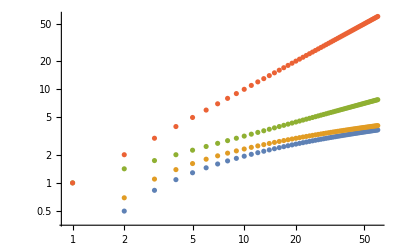

```mathematica
ListLogLogPlot[{Table[-1+HarmonicNumber[n],{n,1,60}],Table[Log[n],{n,1,60}],Table[√n,{n,1,60}],Table[n,{n,1,60}]}]
```

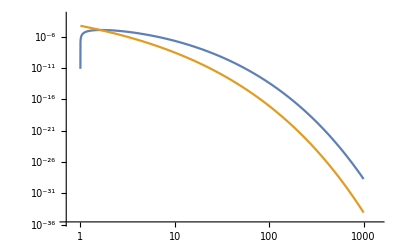

```mathematica
LogLogPlot[{n^(3/2)Log[n] ⅇ^(-π^2 n^0.3),ⅇ^(-π^2 n^0.3)},{n,1,1000}]
```

### Discretisation error for (∑ - ∫ )[P(W < g | W = x)]

We still have to estimate the error in summing over starting position as compared to integrating  P(W<g | W = x)

```mathematica
Assuming[t > 0 && Element[t, Reals]&& Element[b, Reals]&& Element[z, Reals]&& Element[s, Reals],FourierTransform[(Erfc[-1/(√2)(b t + z/t)] - ⅇ^(-2z b)Erfc[-1/(√2)(b t - z/t)])If[z>0,1,0],z,s,FourierParameters->{0,-2Pi}]]
```

DiracDelta[s]+1/(2 π s (-ⅈ b+π s))ⅇ^(-2 π s (-ⅈ b+2 π s) t^2) (-b ⅇ^(2 π^2 s^2 t^2)-b ⅇ^(2 π s (-ⅈ b+2 π s) t^2)-2 ⅈ ⅇ^(2 π^2 s^2 t^2) π s-b ⅇ^(2 π s (-ⅈ b+2 π s) t^2) Erf[(b t)/(√2)]+ⅇ^(2 π^2 s^2 t^2) (b+2 ⅈ π s) Erf[((b+2 ⅈ π s) t)/(√2)])

```mathematica
DiracDelta[s]+1/(2 π s (-ⅈ b+π s))ⅇ^(-2 π s (-ⅈ b+2 π s) t^2) (-b ⅇ^(2 π^2 s^2 t^2)-b ⅇ^(2 π s (-ⅈ b+2 π s) t^2)-2 ⅈ ⅇ^(2 π^2 s^2 t^2) π s-b ⅇ^(2 π s (-ⅈ b+2 π s) t^2) Erf[(b t)/(√2)]+ⅇ^(2 π^2 s^2 t^2) (b+2 ⅈ π s) Erf[((b+2 ⅈ π s) t)/(√2)]) //FullSimplify
```

DiracDelta[s]+(b (-2+Erfc[(b t)/(√2)])-ⅇ^(-2 π s (-ⅈ b+π s) t^2) (b+2 ⅈ π s) Erfc[((b+2 ⅈ π s) t)/(√2)])/(2 π s (-ⅈ b+π s))

```mathematica
Manipulate[LogLogPlot[{
Abs[DiracDelta[s]+(b (-2+Erfc[(b t)/(√2)])-ⅇ^(-2 π s (-ⅈ b+π s) t^2) (b+2 ⅈ π s) Erfc[((b+2 ⅈ π s) t)/(√2)])/(2 π s (-ⅈ b+π s))],
Abs[Re[DiracDelta[s]+(b (-2+Erfc[(b t)/(√2)])-ⅇ^(-2 π s (-ⅈ b+π s) t^2) (b+2 ⅈ π s) Erfc[((b+2 ⅈ π s) t)/(√2)])/(2 π s (-ⅈ b+π s))]],
1/s^2
},{s,1,10}],{t,0.1,1},{{b,0},-1,1}]
```

```mathematica
Assuming[h >0 &&n>0 &&g>0 && Element[h, Reals]&& Element[Kc, Reals] && Element[g, Reals]&& Element[x0, Reals]&& Element[x2, Reals] && Element[n, Reals],FourierTransform[f4e[t],t,s,FourierParameters->{0,-2Pi}]]
```

```mathematica
FourierTransform[Erf[z]If[z<1,1,0],z,s]
```

(-π DiracDelta[s]+((2 DawsonF[s/2])/(√π)-ⅈ ⅇ^(-s^2/4) (-1+ⅇ^(1/4 s (4 ⅈ+s)) Erf[1]-Erf[1-(ⅈ s)/2]-ⅈ Erfi[s/2]))/s)/(√(2 π))

```mathematica
Assuming[t > 0 && Element[t, Reals]&& Element[b, Reals]&& Element[d, Reals]&& Element[z, Reals]&& Element[s, Reals],FourierTransform[(Erfc[-1/(√2)(b t + z/t)] - ⅇ^(-2z b)Erfc[-1/(√2)(b t - z/t)])z PDF[NormalDistribution[0,1/(√n)],z + d] If[z>0,1,0],z,s,FourierParameters->{0,-2Pi}]]
```

$Aborted

```mathematica
Assuming[t > 0 && Element[t, Reals]&& Element[b, Reals]&& Element[d, Reals]&& Element[z, Reals]&& Element[s, Reals],FourierTransform[z^2 PDF[NormalDistribution[0,1/(√n)],z ] If[z>0,1,0],z,s,FourierParameters->{0,-2Pi}]]
```

1/(2 n^2 √π)ⅇ^(-(2 π^2 s^2)/n) (n √π-2 ⅈ √2 ⅇ^((2 π^2 s^2)/n) √n π s-4 π^(5/2) s^2-2 ⅈ ⅇ^((2 π^2 s^2)/n) n DawsonF[(√2 π s)/(√n)]+8 ⅈ ⅇ^((2 π^2 s^2)/n) π^2 s^2 DawsonF[(√2 π s)/(√n)])

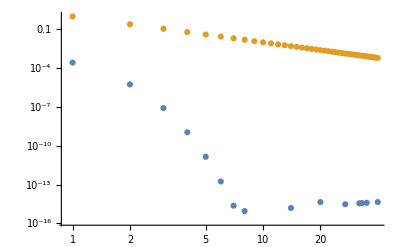

```mathematica
ListLogLogPlot[{Table[1-(Total[Table[PDF[NormalDistribution[0,1/(√n)],x]*1/n,{x,-3,3,1/n}]])^n//N,{n,1,40}],
Table[1/n^2,{n,1,40}]}]
```

### Linear boundary θ shifting

```mathematica
f[d_]:=(1-Exp[-2n(g + Kc/n-x2)(d + θ)])PDF[NormalDistribution[0,1/(√n)],g - (d + θ) -x2](1-Exp[-2n(g-Kc/n-x0)(d + θ)])PDF[NormalDistribution[0,1/(√n)],g-(d+θ)-x0]If[d +θ>0,1,0]
```

```mathematica
Timing[
Assuming[n>0 &&g>0&&Kc>0&&θ >0&& Element[θ, Reals]  && Element[g, Reals]&& Element[x0, Reals] && Element[z, Reals] && Element[x2, Reals]&& Element[n, Reals] && Element[s, Reals],
FourierTransform[f[d],d,s,FourierParameters->{0,-2Pi}]]
]
```

{144.625,(ⅇ^(-g^2 n-2 ⅈ g π s-(2 ⅈ Kc π s)/n-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-Kc x2-ⅈ π s x2-(n x0 x2)/2-(n x2^2)/4+2 ⅈ π s θ) √n (-ⅇ^(Kc^2/n+2 ⅈ g π s+(4 ⅈ Kc π s)/n+Kc x0+g n x0+2 ⅈ π s x0+g n x2) √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2)-ⅇ^(Kc^2/n+2 ⅈ g π s+Kc x0+g n x0+g n x2+2 ⅈ π s x2) √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2)+ⅇ^(g^2 n+4 ⅈ g π s+(2 ⅈ Kc π s)/n+Kc x2+n x0 x2) √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2)+ⅇ^(g^2 n+(2 ⅈ Kc π s)/n+2 ⅈ π s x0+Kc x2+2 ⅈ π s x2+n x0 x2) √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2)-2 ⅇ^(Kc^2/n+2 ⅈ g π s+Kc x0+g n x0+g n x2+2 ⅈ π s x2) Kc √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc-2 ⅈ π s+n (x0-x2))^2))/(2 √n)]+2 ⅈ ⅇ^(Kc^2/n+2 ⅈ g π s+Kc x0+g n x0+g n x2+2 ⅈ π s x2) π s √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc-2 ⅈ π s+n (x0-x2))^2))/(2 √n)]-ⅇ^(Kc^2/n+2 ⅈ g π s+Kc x0+g n x0+g n x2+2 ⅈ π s x2) n x0 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc-2 ⅈ π s+n (x0-x2))^2))/(2 √n)]+ⅇ^(Kc^2/n+2 ⅈ g π s+Kc x0+g n x0+g n x2+2 ⅈ π s x2) n x2 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc-2 ⅈ π s+n (x0-x2))^2))/(2 √n)]+2 ⅇ^(Kc^2/n+2 ⅈ g π s+(4 ⅈ Kc π s)/n+Kc x0+g n x0+2 ⅈ π s x0+g n x2) Kc √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc+2 ⅈ π s+n (x0-x2))^2))/(2 √n)]+2 ⅈ ⅇ^(Kc^2/n+2 ⅈ g π s+(4 ⅈ Kc π s)/n+Kc x0+g n x0+2 ⅈ π s x0+g n x2) π s √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc+2 ⅈ π s+n (x0-x2))^2))/(2 √n)]+ⅇ^(Kc^2/n+2 ⅈ g π s+(4 ⅈ Kc π s)/n+Kc x0+g n x0+2 ⅈ π s x0+g n x2) n x0 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc+2 ⅈ π s+n (x0-x2))^2))/(2 √n)]-ⅇ^(Kc^2/n+2 ⅈ g π s+(4 ⅈ Kc π s)/n+Kc x0+g n x0+2 ⅈ π s x0+g n x2) n x2 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc+2 ⅈ π s+n (x0-x2))^2))/(2 √n)]-2 ⅇ^(g^2 n+4 ⅈ g π s+(2 ⅈ Kc π s)/n+Kc x2+n x0 x2) g n √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]-2 ⅈ ⅇ^(g^2 n+4 ⅈ g π s+(2 ⅈ Kc π s)/n+Kc x2+n x0 x2) π s √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]+ⅇ^(g^2 n+4 ⅈ g π s+(2 ⅈ Kc π s)/n+Kc x2+n x0 x2) n x0 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]+ⅇ^(g^2 n+4 ⅈ g π s+(2 ⅈ Kc π s)/n+Kc x2+n x0 x2) n x2 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]+2 ⅇ^(g^2 n+(2 ⅈ Kc π s)/n+2 ⅈ π s x0+Kc x2+2 ⅈ π s x2+n x0 x2) g n √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-2 ⅈ ⅇ^(g^2 n+(2 ⅈ Kc π s)/n+2 ⅈ π s x0+Kc x2+2 ⅈ π s x2+n x0 x2) π s √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(g^2 n+(2 ⅈ Kc π s)/n+2 ⅈ π s x0+Kc x2+2 ⅈ π s x2+n x0 x2) n x0 √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(g^2 n+(2 ⅈ Kc π s)/n+2 ⅈ π s x0+Kc x2+2 ⅈ π s x2+n x0 x2) n x2 √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]))/(4 √π √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2))}

```mathematica
(ⅇ^(-g^2 n-2 ⅈ g π s-(2 ⅈ Kc π s)/n-(π^2 s^2)/n-ⅈ π s x0-(n x0^2)/4-Kc x2-ⅈ π s x2-(n x0 x2)/2-(n x2^2)/4+2 ⅈ π s θ) √n (-ⅇ^(Kc^2/n+2 ⅈ g π s+(4 ⅈ Kc π s)/n+Kc x0+g n x0+2 ⅈ π s x0+g n x2) √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2)-ⅇ^(Kc^2/n+2 ⅈ g π s+Kc x0+g n x0+g n x2+2 ⅈ π s x2) √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2)+ⅇ^(g^2 n+4 ⅈ g π s+(2 ⅈ Kc π s)/n+Kc x2+n x0 x2) √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2)+ⅇ^(g^2 n+(2 ⅈ Kc π s)/n+2 ⅈ π s x0+Kc x2+2 ⅈ π s x2+n x0 x2) √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2)-2 ⅇ^(Kc^2/n+2 ⅈ g π s+Kc x0+g n x0+g n x2+2 ⅈ π s x2) Kc √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc-2 ⅈ π s+n (x0-x2))^2))/(2 √n)]+2 ⅈ ⅇ^(Kc^2/n+2 ⅈ g π s+Kc x0+g n x0+g n x2+2 ⅈ π s x2) π s √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc-2 ⅈ π s+n (x0-x2))^2))/(2 √n)]-ⅇ^(Kc^2/n+2 ⅈ g π s+Kc x0+g n x0+g n x2+2 ⅈ π s x2) n x0 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc-2 ⅈ π s+n (x0-x2))^2))/(2 √n)]+ⅇ^(Kc^2/n+2 ⅈ g π s+Kc x0+g n x0+g n x2+2 ⅈ π s x2) n x2 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc-2 ⅈ π s+n (x0-x2))^2))/(2 √n)]+2 ⅇ^(Kc^2/n+2 ⅈ g π s+(4 ⅈ Kc π s)/n+Kc x0+g n x0+2 ⅈ π s x0+g n x2) Kc √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc+2 ⅈ π s+n (x0-x2))^2))/(2 √n)]+2 ⅈ ⅇ^(Kc^2/n+2 ⅈ g π s+(4 ⅈ Kc π s)/n+Kc x0+g n x0+2 ⅈ π s x0+g n x2) π s √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc+2 ⅈ π s+n (x0-x2))^2))/(2 √n)]+ⅇ^(Kc^2/n+2 ⅈ g π s+(4 ⅈ Kc π s)/n+Kc x0+g n x0+2 ⅈ π s x0+g n x2) n x0 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc+2 ⅈ π s+n (x0-x2))^2))/(2 √n)]-ⅇ^(Kc^2/n+2 ⅈ g π s+(4 ⅈ Kc π s)/n+Kc x0+g n x0+2 ⅈ π s x0+g n x2) n x2 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 Kc+2 ⅈ π s+n (x0-x2))^2))/(2 √n)]-2 ⅇ^(g^2 n+4 ⅈ g π s+(2 ⅈ Kc π s)/n+Kc x2+n x0 x2) g n √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]-2 ⅈ ⅇ^(g^2 n+4 ⅈ g π s+(2 ⅈ Kc π s)/n+Kc x2+n x0 x2) π s √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]+ⅇ^(g^2 n+4 ⅈ g π s+(2 ⅈ Kc π s)/n+Kc x2+n x0 x2) n x0 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]+ⅇ^(g^2 n+4 ⅈ g π s+(2 ⅈ Kc π s)/n+Kc x2+n x0 x2) n x2 √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)]+2 ⅇ^(g^2 n+(2 ⅈ Kc π s)/n+2 ⅈ π s x0+Kc x2+2 ⅈ π s x2+n x0 x2) g n √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-2 ⅈ ⅇ^(g^2 n+(2 ⅈ Kc π s)/n+2 ⅈ π s x0+Kc x2+2 ⅈ π s x2+n x0 x2) π s √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(g^2 n+(2 ⅈ Kc π s)/n+2 ⅈ π s x0+Kc x2+2 ⅈ π s x2+n x0 x2) n x0 √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]-ⅇ^(g^2 n+(2 ⅈ Kc π s)/n+2 ⅈ π s x0+Kc x2+2 ⅈ π s x2+n x0 x2) n x2 √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2) Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)]))/(4 √π √((2 g n-2 ⅈ π s-n x0-n x2)^2) √((2 g n+2 ⅈ π s-n x0-n x2)^2) √((2 Kc-2 ⅈ π s+n x0-n x2)^2) √((2 Kc+2 ⅈ π s+n x0-n x2)^2))//Simplify
```

1/(4 √π)ⅇ^(-(π^2 s^2)/n-1/4 n (x0+x2)^2-ⅈ π s (x0+x2-2 θ)) √n (ⅇ^(2 ⅈ g π s+n x0 x2)-ⅇ^(Kc^2/n-g^2 n+2 ⅈ π s x0+Kc ((2 ⅈ π s)/n+x0-x2)+g n (x0+x2))-ⅇ^(Kc^2/n-g^2 n+Kc (-(2 ⅈ π s)/n+x0-x2)+2 ⅈ π s x2+g n (x0+x2))+ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2))-(ⅇ^(Kc^2/n-g^2 n+Kc (-(2 ⅈ π s)/n+x0-x2)+2 ⅈ π s x2+g n (x0+x2)) √((2 Kc-2 ⅈ π s+n (x0-x2))^2) Erf[(√((2 Kc-2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 Kc-2 ⅈ π s+n (x0-x2))+(ⅇ^(Kc^2/n-g^2 n+2 ⅈ π s x0+Kc ((2 ⅈ π s)/n+x0-x2)+g n (x0+x2)) √((2 Kc+2 ⅈ π s+n (x0-x2))^2) Erf[(√((2 Kc+2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 Kc+2 ⅈ π s+n (x0-x2))-(2 ⅇ^(2 ⅈ g π s+n x0 x2) g n Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))-(2 ⅈ ⅇ^(2 ⅈ g π s+n x0 x2) π s Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(ⅇ^(2 ⅈ g π s+n x0 x2) n x0 Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(ⅇ^(2 ⅈ g π s+n x0 x2) n x2 Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(2 ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) g n Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(2 ⅈ ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) π s Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) n x0 Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) n x2 Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2)))

```mathematica
1/(4 √π)ⅇ^(-(π^2 s^2)/n-1/4 n (x0+x2)^2-ⅈ π s (x0+x2-2 θ)) √n (ⅇ^(2 ⅈ g π s+n x0 x2)-ⅇ^(Kc^2/n-g^2 n+2 ⅈ π s x0+Kc ((2 ⅈ π s)/n+x0-x2)+g n (x0+x2))-ⅇ^(Kc^2/n-g^2 n+Kc (-(2 ⅈ π s)/n+x0-x2)+2 ⅈ π s x2+g n (x0+x2))+ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2))-(ⅇ^(Kc^2/n-g^2 n+Kc (-(2 ⅈ π s)/n+x0-x2)+2 ⅈ π s x2+g n (x0+x2)) √((2 Kc-2 ⅈ π s+n (x0-x2))^2) Erf[(√((2 Kc-2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 Kc-2 ⅈ π s+n (x0-x2))+(ⅇ^(Kc^2/n-g^2 n+2 ⅈ π s x0+Kc ((2 ⅈ π s)/n+x0-x2)+g n (x0+x2)) √((2 Kc+2 ⅈ π s+n (x0-x2))^2) Erf[(√((2 Kc+2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 Kc+2 ⅈ π s+n (x0-x2))-(2 ⅇ^(2 ⅈ g π s+n x0 x2) g n Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))-(2 ⅈ ⅇ^(2 ⅈ g π s+n x0 x2) π s Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(ⅇ^(2 ⅈ g π s+n x0 x2) n x0 Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(ⅇ^(2 ⅈ g π s+n x0 x2) n x2 Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(2 ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) g n Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(2 ⅈ ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) π s Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) n x0 Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) n x2 Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2)))/. θ->0
```

1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √n (ⅇ^(2 ⅈ g π s+n x0 x2)-ⅇ^(Kc^2/n-g^2 n+2 ⅈ π s x0+Kc ((2 ⅈ π s)/n+x0-x2)+g n (x0+x2))-ⅇ^(Kc^2/n-g^2 n+Kc (-(2 ⅈ π s)/n+x0-x2)+2 ⅈ π s x2+g n (x0+x2))+ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2))-(ⅇ^(Kc^2/n-g^2 n+Kc (-(2 ⅈ π s)/n+x0-x2)+2 ⅈ π s x2+g n (x0+x2)) √((2 Kc-2 ⅈ π s+n (x0-x2))^2) Erf[(√((2 Kc-2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 Kc-2 ⅈ π s+n (x0-x2))+(ⅇ^(Kc^2/n-g^2 n+2 ⅈ π s x0+Kc ((2 ⅈ π s)/n+x0-x2)+g n (x0+x2)) √((2 Kc+2 ⅈ π s+n (x0-x2))^2) Erf[(√((2 Kc+2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 Kc+2 ⅈ π s+n (x0-x2))-(2 ⅇ^(2 ⅈ g π s+n x0 x2) g n Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))-(2 ⅈ ⅇ^(2 ⅈ g π s+n x0 x2) π s Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(ⅇ^(2 ⅈ g π s+n x0 x2) n x0 Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(ⅇ^(2 ⅈ g π s+n x0 x2) n x2 Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(2 ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) g n Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(2 ⅈ ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) π s Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) n x0 Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) n x2 Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2)))

```mathematica
Manipulate[LogLogPlot[
Abs[1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √n (ⅇ^(2 ⅈ g π s+n x0 x2)-ⅇ^(Kc^2/n-g^2 n+2 ⅈ π s x0+Kc ((2 ⅈ π s)/n+x0-x2)+g n (x0+x2))-ⅇ^(Kc^2/n-g^2 n+Kc (-(2 ⅈ π s)/n+x0-x2)+2 ⅈ π s x2+g n (x0+x2))+ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2))-(ⅇ^(Kc^2/n-g^2 n+Kc (-(2 ⅈ π s)/n+x0-x2)+2 ⅈ π s x2+g n (x0+x2)) √((2 Kc-2 ⅈ π s+n (x0-x2))^2) Erf[(√((2 Kc-2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 Kc-2 ⅈ π s+n (x0-x2))+(ⅇ^(Kc^2/n-g^2 n+2 ⅈ π s x0+Kc ((2 ⅈ π s)/n+x0-x2)+g n (x0+x2)) √((2 Kc+2 ⅈ π s+n (x0-x2))^2) Erf[(√((2 Kc+2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 Kc+2 ⅈ π s+n (x0-x2))-(2 ⅇ^(2 ⅈ g π s+n x0 x2) g n Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))-(2 ⅈ ⅇ^(2 ⅈ g π s+n x0 x2) π s Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(ⅇ^(2 ⅈ g π s+n x0 x2) n x0 Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(ⅇ^(2 ⅈ g π s+n x0 x2) n x2 Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(2 ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) g n Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(2 ⅈ ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) π s Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) n x0 Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) n x2 Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2)))],{s,1,90}],{g,0.5,1},{x0,-3,g},{x2,-3,g},{n,1,50,1},{{Kc,0.1},-3,3}]
```

```mathematica
Series[ComplexExpand[Abs[1/(4 √π)ⅇ^(-(π^2 s^2)/n-ⅈ π s (x0+x2)-1/4 n (x0+x2)^2) √n (ⅇ^(2 ⅈ g π s+n x0 x2)-ⅇ^(Kc^2/n-g^2 n+2 ⅈ π s x0+Kc ((2 ⅈ π s)/n+x0-x2)+g n (x0+x2))-ⅇ^(Kc^2/n-g^2 n+Kc (-(2 ⅈ π s)/n+x0-x2)+2 ⅈ π s x2+g n (x0+x2))+ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2))-(ⅇ^(Kc^2/n-g^2 n+Kc (-(2 ⅈ π s)/n+x0-x2)+2 ⅈ π s x2+g n (x0+x2)) √((2 Kc-2 ⅈ π s+n (x0-x2))^2) Erf[(√((2 Kc-2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 Kc-2 ⅈ π s+n (x0-x2))+(ⅇ^(Kc^2/n-g^2 n+2 ⅈ π s x0+Kc ((2 ⅈ π s)/n+x0-x2)+g n (x0+x2)) √((2 Kc+2 ⅈ π s+n (x0-x2))^2) Erf[(√((2 Kc+2 ⅈ π s+n x0-n x2)^2))/(2 √n)])/(2 Kc+2 ⅈ π s+n (x0-x2))-(2 ⅇ^(2 ⅈ g π s+n x0 x2) g n Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))-(2 ⅈ ⅇ^(2 ⅈ g π s+n x0 x2) π s Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(ⅇ^(2 ⅈ g π s+n x0 x2) n x0 Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(ⅇ^(2 ⅈ g π s+n x0 x2) n x2 Erf[(√((2 g n+2 ⅈ π s-n (x0+x2))^2))/(2 √n)])/(√((2 g n+2 ⅈ π s-n (x0+x2))^2))+(2 ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) g n Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(2 ⅈ ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) π s Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) n x0 Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))-(ⅇ^(-2 ⅈ g π s+n x0 x2+2 ⅈ π s (x0+x2)) n x2 Erf[(√((-2 g n+2 ⅈ π s+n (x0+x2))^2))/(2 √n)])/(√((-2 g n+2 ⅈ π s+n (x0+x2))^2)))]],{s,∞,3}]
```

$Aborted

## ∑_(k=2)^(n-2) E_(k,h) = ∑_(k=2)^(n-2) I_k J_k

```mathematica
I1[k_,n_,g_]:=n^(3/2)/k^(5/2)(g^2+1)ⅇ^((-n g^2)/(2k))
```

```mathematica
J1[k_,n_,Kc_]:= (√(n/(n-k-1))+Kc)1/n
```

```mathematica
eIJ[n_]:=∑_(k=2)^(n-2) I1[k,n,1]J1[k,n,1]
```

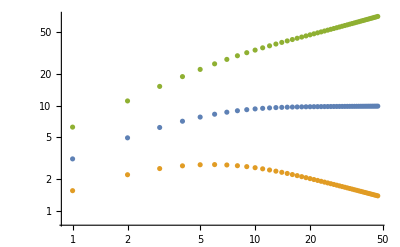

```mathematica
ListLogLogPlot[{Table[eIJ[n] n //N,{n,4,50}],Table[eIJ[n] √n //N,{n,4,50}],Table[eIJ[n] n^(3/2) //N,{n,4,50}]}]
```

```mathematica
I2[k_,n_,g_]:=√(n/k)(g^2/k^2+1/n +1/(n √n)+g/(k n)+1/n^2)ⅇ^((-n g^2)/(2k))
```

```mathematica
eIJ2[n_]:=∑_(k=2)^(n-2) I2[k,n,1]J1[k,n,1]
```

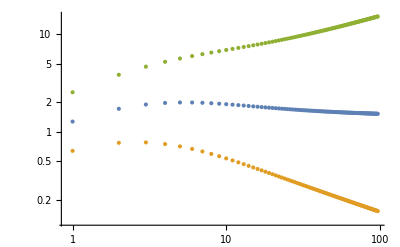

```mathematica
ListLogLogPlot[{Table[eIJ2[n] n //N,{n,4,100}],Table[eIJ2[n] √n //N,{n,4,100}],Table[eIJ2[n] n^(3/2) //N,{n,4,100}]}]
```

## Convolution decomposition

The Fourier Convolution theorem states for f,g in L^1 that FT[f  dot g] = FT[f]*FT[g] (s) = ∫  f̂(t) ĝ(s-t) ⅆt

```mathematica
f[y_]:=PDF[NormalDistribution[0,1/(√n)],g2 -y  -x]
g[y_]:=(1 - ⅇ^(-2n y(g1 - x)))
```

```mathematica
FourierTransform[f[y],y,s,FourierParameters->{0, -2*Pi}]
```

ⅇ^(-(2 π s (ⅈ g2 n+π s-ⅈ n x))/n)

```mathematica
Plot[Abs[ⅇ^(-(2 π s (ⅈ g2 n+π s-ⅈ n x))/n)]]
```

```mathematica
FourierTransform[g[y]If[y>0,1,0],y,s,FourierParameters->{0, -2*Pi}]
```

(g1 n-n x)/(2 ⅈ g1 n π s-2 π^2 s^2-2 ⅈ n π s x)

```mathematica
Manipulate[LogPlot[{
Abs[ⅇ^(-(2 π s (ⅈ g2 n+π s-ⅈ n x))/n)],Abs[(g1 n-n x)/(2 ⅈ g1 n π s-2 π^2 s^2-2 ⅈ n π s x)]},{s,-9,9}, PlotRange->Full, PlotLabel->"FT upper bound", PlotLegends->{"Polynomial part","exp part","ABS FT","Re FT"},PlotStyle->{Blue,Blue,Red,Dashed}],{{n,46},1,50},{{x,0.157},-3,g1},{g1,0.5,3},{g2,0.5,3},ControlPlacement->Left]
```

```mathematica
ComplexExpand[Abs[(g1 n-n x)/(2 ⅈ g1 n π s-2 π^2 s^2-2 ⅈ n π s x)]]//Simplify
```

(√((g1 n-n x)^2))/(√(4 π^4 s^4+(2 g1 n π s-2 n π s x)^2))

```mathematica
(n(g1 -x))/(√(4 π^4 s^4+(2π s n ( g1  -   x))^2))
```

```mathematica
Manipulate[LogPlot[{
ⅇ^(-(2 π^2 s^2)/n),(n(g1 -x))/(√(4 π^4 s^4+(2π s n ( g1  -   x))^2))},{s,-9,9}, PlotRange->Full, PlotLabel->"FT upper bound", PlotLegends->{"Polynomial part","exp part","ABS FT","Re FT"},PlotStyle->{Blue,Blue,Red,Dashed}],{{n,46},1,50},{{x,0.157},-3,g1},{g1,0.5,3},{g2,0.5,3},ControlPlacement->Left]
```

```mathematica
Manipulate[LogPlot[{
ⅇ^(-(2 π^2 s^2)/n),(n(g1 -x))/(√(4 π^4 (t-s)^4+(2π (t-s) n ( g1  -   x))^2)),ⅇ^(-(2 π^2 s^2)/n)*(n(g1 -x))/(√(4 π^4 (t-s)^4+(2π (t-s) n ( g1  -   x))^2))},{s,-9,9}, PlotRange->Full, PlotLabel->"FT upper bound", PlotLegends->{"Polynomial part","exp part","ABS FT","Re FT"},PlotStyle->{Blue,Blue,Red,Dashed}],{{n,46},1,50},{{x,0.157},-3,g1},{g1,0.5,3},{g2,0.5,3},{t,-5,5},ControlPlacement->Left]
```

```mathematica
h[t_,n_,g1_,x_]:=NIntegrate[ⅇ^(-(2 π^2 s^2)/n)*(n(g1 -x))/(√(4 π^4 (t-s)^4+(2π (t-s) n ( g1  -   x))^2)),{s,-∞,∞}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {0.99228}. NIntegrate obtained 0.22007 and 0.0222494 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in s near {s} = {1.99429}. NIntegrate obtained 0.0370939 and 1.48351×10^-6 for the integral and error estimates.

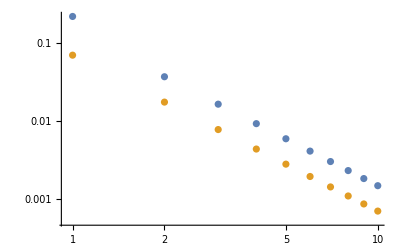

```mathematica
ListLogLogPlot[{
Table[h[t,6,0.5,0],{t,1,10}],
Table[6/(2 π^2 t^2)(0.5)PDF[NormalDistribution[0,1/(√6)],0.5],{t,1,10}]}]
```

```mathematica
Manipulate[
LogLogPlot[{
h[k n^a,n,g1,x],
Abs[1/2 ⅇ^(-2 g1 n (g2+x)-(2 π s (π s+ⅈ n (g2+x-θ)))/n) (ⅇ^(4 ⅈ π s x+2 g1 n (g2+x)) Erfc[(-g2 n+2 ⅈ π s+n x)/(√2 √n)]+ⅇ^(2 g1^2 n+4 ⅈ g1 π s+2 g2 n x) (-2+Erfc[(-2 ⅈ π s+n (-2 g1+g2+x))/(√2 √n)]))]/.s-> k n^a /. θ-> 0
}
,{n,1,200}, PlotRange->Full, PlotLabel->"True vs Approximation", PlotLegends->{"Vin upper bound","True error"}],{x,-3,g1},{g1,0.5,3},{g2,0.5,3},{k,1,20,1},{a,0.5,1},ControlPlacement->Left]
```

## Symmetrisation

```mathematica
FourierTransform[f[y],y,s,FourierParameters->{0, -2*Pi}]
```

FourierTransform[f[y],y,s,FourierParameters→{0,-2 π}]

```mathematica
f[dy_]:=PDF[NormalDistribution[0,1/(√n)],gy - gx +dx - dy  ]PDF[NormalDistribution[0,1/(√n)],gy - gz +dz - dy  ](1 - ⅇ^(-2n dy dx))(1 - ⅇ^(-2n dy dz))
```

Force the function to be symmetric. The error arising from quadrature should be exactly half of the Fourier transform of the symmetrised function.

```mathematica
Manipulate[Plot[{PDF[NormalDistribution[0,1/(√n)],gy - gx +dx - dy  ]PDF[NormalDistribution[0,1/(√n)],gy - gz +dz - dy  ](1 - ⅇ^(-2n dy dx))(1 - ⅇ^(-2n dy dz)),
PDF[NormalDistribution[0,1/(√n)],gy - gx +dx - dy  ]PDF[NormalDistribution[0,1/(√n)],gy - gz +dz - dy  ](1 - ⅇ^(-2n dy dx))(1 - ⅇ^(-2n dy dz))If[dy>0,1,0]+
PDF[NormalDistribution[0,1/(√n)],gy - gx +dx + dy  ]PDF[NormalDistribution[0,1/(√n)],gy - gz +dz + dy  ](1 - ⅇ^(2n dy dx))(1 - ⅇ^(2n dy dz))If[dy<0,1,0]},{dy,-3,3}],{n,1,10},{gx,0.5,1},{gy,0.5,1},{gz,0.5,1},{dx,0,3},{dz,0,3}]
```

```mathematica
Evaluate[D[PDF[NormalDistribution[0,1/(√n)],gy - gx +dx - dy  ]PDF[NormalDistribution[0,1/(√n)],gy - gz +dz - dy  ](1 - ⅇ^(-2n dy dx))(1 - ⅇ^(-2n dy dz)),{dy,3}]]/. dy-> 0
```

-(12 dx dz^2 ⅇ^(-1/2 (dx-gx+gy)^2 n-1/2 (dz+gy-gz)^2 n) n^4)/π+(6 dz n^2 (-2 dx^2 ⅇ^(-1/2 (dx-gx+gy)^2 n-1/2 (dz+gy-gz)^2 n) n^2+2 dx ⅇ^(-1/2 (dx-gx+gy)^2 n-1/2 (dz+gy-gz)^2 n) n ((dx-gx+gy) n+(dz+gy-gz) n)))/π

```mathematica
Evaluate[D[PDF[NormalDistribution[0,1/(√n)],gy - gx +dx + dy  ]PDF[NormalDistribution[0,1/(√n)],gy - gz +dz + dy  ](1 - ⅇ^(2n dy dx))(1 - ⅇ^(2n dy dz)),{dy,3}]]/. dy-> 0
```

(12 dx dz^2 ⅇ^(-1/2 (dx-gx+gy)^2 n-1/2 (dz+gy-gz)^2 n) n^4)/π-(6 dz n^2 (-2 dx^2 ⅇ^(-1/2 (dx-gx+gy)^2 n-1/2 (dz+gy-gz)^2 n) n^2-2 dx ⅇ^(-1/2 (dx-gx+gy)^2 n-1/2 (dz+gy-gz)^2 n) n (-(dx-gx+gy) n-(dz+gy-gz) n)))/π